```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,t,0]],B:=Inverse[β[ω,0.001,t,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,3000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]
```

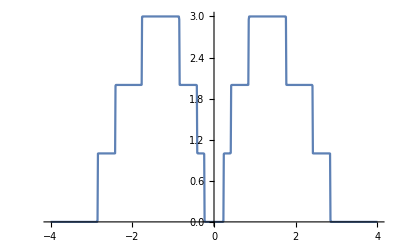

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
tr50[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],T=},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{i=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[i,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],gg}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[T].J.T].c],100]; J=J]; Il1:=Inverse[IdentityMatrix[14]-sl1.TT[1].SR[ω,0.001,t,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];
η]
```

```mathematica
Export["50imp7.csv",%168]
```

50imp7.csv

```mathematica
Table[{ω,Mean[Table[tr50[ω,0.001,t,0,0.7],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000546916},{0.01,0.0000438348},{0.02,0.0000385163},{0.03,0.0000401327},{0.04,0.0000528631},{0.05,0.0000750199},{0.06,0.00011624},{0.07,0.000155039},{0.08,0.000215326},{0.09,0.000286202},{0.1,0.000368295},{0.11,0.000467509},{0.12,0.000615624},{0.13,0.000765239},{0.14,0.00100828},{0.15,0.00124047},{0.16,0.00161473},{0.17,0.00210356},{0.18,0.00278342},{0.19,0.00371369},{0.2,0.0049719},{0.21,0.00736976},{0.22,0.0119294},{0.23,0.0251129},{0.24,0.0892294},{0.25,0.219381},{0.26,0.390204},{0.27,0.465354},{0.28,0.514168},{0.29,0.547117},{0.3,0.566322},{0.31,0.577421},{0.32,0.576707},{0.33,0.595039},{0.34,0.609285},{0.35,0.607234},{0.36,0.606839},{0.37,0.607411},{0.38,0.592531},{0.39,0.589231},{0.4,0.556913},{0.41,0.511479},{0.42,0.637298},{0.43,0.667602},{0.44,0.683966},{0.45,0.669505},{0.46,0.682918},{0.47,0.714196},{0.48,0.730206},{0.49,0.762654},{0.5,0.806662},{0.51,0.820588},{0.52,0.859546},{0.53,0.888161},{0.54,0.893545},{0.55,0.933305},{0.56,0.951595},{0.57,0.988427},{0.58,0.991199},{0.59,1.01564},{0.6,1.03242},{0.61,1.03818},{0.62,1.06877},{0.63,1.05908},{0.64,1.09459},{0.65,1.11468},{0.66,1.11625},{0.67,1.11351},{0.68,1.13176},{0.69,1.14538},{0.7,1.15182},{0.71,1.16594},{0.72,1.1594},{0.73,1.17688},{0.74,1.19092},{0.75,1.18406},{0.76,1.20579},{0.77,1.21653},{0.78,1.21217},{0.79,1.22684},{0.8,1.22576},{0.81,1.22946},{0.82,1.23037},{0.83,1.20863},{0.84,1.11882},{0.85,0.867765},{0.86,0.872174},{0.87,0.84363},{0.88,0.86908},{0.89,0.906847},{0.9,1.00474},{0.91,1.0491},{0.92,1.12706},{0.93,1.18455},{0.94,1.24349},{0.95,1.30998},{0.96,1.34926},{0.97,1.39747},{0.98,1.47179},{0.99,1.49389},{1.,1.52605},{1.01,1.6704},{1.02,1.64499},{1.03,1.59218},{1.04,1.4803},{1.05,1.3023},{1.06,1.05861},{1.07,0.836672},{1.08,0.591782},{1.09,0.487103},{1.1,0.488414},{1.11,0.525741},{1.12,0.59777},{1.13,0.624481},{1.14,0.676889},{1.15,0.70473},{1.16,0.741047},{1.17,0.788605},{1.18,0.823774},{1.19,0.85235},{1.2,0.873164},{1.21,0.8936},{1.22,0.92252},{1.23,0.956392},{1.24,0.949947},{1.25,0.98077},{1.26,0.975865},{1.27,0.995668},{1.28,1.00436},{1.29,1.00415},{1.3,1.024},{1.31,1.03111},{1.32,1.03279},{1.33,1.04055},{1.34,1.04692},{1.35,1.05401},{1.36,1.0578},{1.37,1.0544},{1.38,1.05479},{1.39,1.05971},{1.4,1.07453},{1.41,1.07725},{1.42,1.06394},{1.43,1.0465},{1.44,1.05408},{1.45,1.06303},{1.46,1.06628},{1.47,1.05147},{1.48,1.05056},{1.49,1.0366},{1.5,1.03975},{1.51,1.05703},{1.52,1.03082},{1.53,1.02283},{1.54,1.02926},{1.55,1.01052},{1.56,1.01251},{1.57,0.991167},{1.58,0.979863},{1.59,0.966319},{1.6,0.963215},{1.61,0.937518},{1.62,0.939398},{1.63,0.932361},{1.64,0.89663},{1.65,0.871709},{1.66,0.858652},{1.67,0.831273},{1.68,0.798509},{1.69,0.773554},{1.7,0.745456},{1.71,0.718071},{1.72,0.680524},{1.73,0.653364},{1.74,0.679312},{1.75,0.801729},{1.76,1.31103},{1.77,2.46673},{1.78,1.95339},{1.79,2.11635},{1.8,2.19303},{1.81,1.77276},{1.82,1.19926},{1.83,0.923784},{1.84,0.738682},{1.85,0.654093},{1.86,0.611066},{1.87,0.626551},{1.88,0.651878},{1.89,0.67226},{1.9,0.696275},{1.91,0.716501},{1.92,0.726958},{1.93,0.742587},{1.94,0.764531},{1.95,0.763945},{1.96,0.787967},{1.97,0.774649},{1.98,0.768221},{1.99,0.809368},{2.,0.799162},{2.01,0.806089},{2.02,0.824294},{2.03,0.805311},{2.04,0.817694},{2.05,0.815996},{2.06,0.821414},{2.07,0.813497},{2.08,0.81353},{2.09,0.80839},{2.1,0.812196},{2.11,0.813807},{2.12,0.808955},{2.13,0.806643},{2.14,0.794095},{2.15,0.800765},{2.16,0.786456},{2.17,0.806334},{2.18,0.800929},{2.19,0.782016},{2.2,0.755893},{2.21,0.775602},{2.22,0.775952},{2.23,0.753071},{2.24,0.765019},{2.25,0.753136},{2.26,0.739695},{2.27,0.731195},{2.28,0.728169},{2.29,0.719371},{2.3,0.700792},{2.31,0.686533},{2.32,0.674141},{2.33,0.656168},{2.34,0.648332},{2.35,0.629347},{2.36,0.613336},{2.37,0.576804},{2.38,0.547862},{2.39,0.534421},{2.4,0.516472},{2.41,0.679464},{2.42,1.3839},{2.43,1.43172},{2.44,1.18821},{2.45,1.22116},{2.46,0.876651},{2.47,0.62801},{2.48,0.452695},{2.49,0.393555},{2.5,0.355595},{2.51,0.348415},{2.52,0.340692},{2.53,0.367345},{2.54,0.3664},{2.55,0.370696},{2.56,0.379052},{2.57,0.363863},{2.58,0.381842},{2.59,0.37769},{2.6,0.387922},{2.61,0.386658},{2.62,0.396843},{2.63,0.387805},{2.64,0.394127},{2.65,0.390811},{2.66,0.394016},{2.67,0.389183},{2.68,0.389165},{2.69,0.384751},{2.7,0.395706},{2.71,0.391494},{2.72,0.37733},{2.73,0.379578},{2.74,0.379862},{2.75,0.376281},{2.76,0.368631},{2.77,0.367069},{2.78,0.361851},{2.79,0.348879},{2.8,0.343641},{2.81,0.335802},{2.82,0.330538},{2.83,0.295172},{2.84,0.288482},{2.85,0.531208},{2.86,2.89504},{2.87,0.428563},{2.88,1.63802},{2.89,0.397408},{2.9,0.180711},{2.91,0.0753806},{2.92,0.0705932},{2.93,0.0156212},{2.94,0.00800968},{2.95,0.00586348},{2.96,0.00394493},{2.97,0.00290064},{2.98,0.00237685},{2.99,0.00178249},{3.,0.00165015},{3.01,0.00116195},{3.02,0.00111529},{3.03,0.000918226},{3.04,0.000850781},{3.05,0.000695865},{3.06,0.000604391},{3.07,0.000491934},{3.08,0.00045379},{3.09,0.000391631},{3.1,0.000383974},{3.11,0.000345109},{3.12,0.000284303},{3.13,0.000263014},{3.14,0.000232381},{3.15,0.000204104},{3.16,0.000180205},{3.17,0.000162649},{3.18,0.000154127},{3.19,0.000140912},{3.2,0.000137839},{3.21,0.0000941593},{3.22,0.000101668},{3.23,0.0000992979},{3.24,0.0000966304},{3.25,0.0000805822},{3.26,0.0000739955},{3.27,0.0000704549},{3.28,0.0000631881},{3.29,0.0000586746},{3.3,0.0000534756},{3.31,0.0000511781},{3.32,0.0000456395},{3.33,0.0000459856},{3.34,0.0000378711},{3.35,0.0000376541},{3.36,0.0000376483},{3.37,0.0000345874},{3.38,0.0000314692},{3.39,0.0000261525},{3.4,0.0000246338},{3.41,0.0000265418},{3.42,0.0000240179},{3.43,0.0000225938},{3.44,0.0000197341},{3.45,0.0000214298},{3.46,0.0000176154},{3.47,0.0000172171},{3.48,0.000017526},{3.49,0.0000153632},{3.5,0.0000140934},{3.51,0.0000133848},{3.52,0.0000135026},{3.53,0.0000119456},{3.54,0.0000103173},{3.55,0.0000115808},{3.56,9.89222×10^-6},{3.57,9.30287×10^-6},{3.58,9.0141×10^-6},{3.59,9.71746×10^-6},{3.6,8.23758×10^-6},{3.61,8.02613×10^-6},{3.62,8.42807×10^-6},{3.63,7.10555×10^-6},{3.64,6.70781×10^-6},{3.65,6.10285×10^-6},{3.66,6.37681×10^-6},{3.67,6.47371×10^-6},{3.68,6.29599×10^-6},{3.69,5.88283×10^-6},{3.7,4.47169×10^-6},{3.71,5.15352×10^-6},{3.72,4.57496×10^-6},{3.73,4.36095×10^-6},{3.74,4.32289×10^-6},{3.75,4.17211×10^-6},{3.76,3.64761×10^-6},{3.77,3.55237×10^-6},{3.78,3.47376×10^-6},{3.79,3.41001×10^-6},{3.8,3.2063×10^-6},{3.81,3.34605×10^-6},{3.82,3.0306×10^-6},{3.83,2.63738×10^-6},{3.84,2.69155×10^-6},{3.85,2.73361×10^-6},{3.86,2.19788×10^-6},{3.87,2.43411×10^-6},{3.88,2.13457×10^-6},{3.89,2.0912×10^-6},{3.9,2.24552×10^-6},{3.91,1.98767×10^-6},{3.92,1.8982×10^-6},{3.93,1.85256×10^-6},{3.94,1.79495×10^-6},{3.95,1.89823×10^-6},{3.96,1.66484×10^-6},{3.97,1.63804×10^-6},{3.98,1.69342×10^-6},{3.99,1.49753×10^-6},{4.,1.46064×10^-6}}

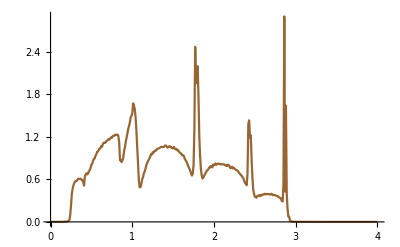

```mathematica
ListPlot[%168,Joined->True,PlotStyle->Brown]
```

```mathematica
Clear[imp]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Module[{imp1=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{1,1}}->ω+ⅈ*δ-ϵ1]]],imp2=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{14,14}}->ω+ⅈ*δ-ϵ1]]],imp7=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{2,2}}->ω+ⅈ*δ-ϵ1]]],imp3=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{13,13}}->ω+ⅈ*δ-ϵ1]]],imp8=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{3,3}}->ω+ⅈ*δ-ϵ1]]],imp4=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{12,12}}->ω+ⅈ*δ-ϵ1]]],imp9=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{4,4}}->ω+ⅈ*δ-ϵ1]]],imp5=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{11,11}}->ω+ⅈ*δ-ϵ1]]],imp10=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{5,5}}->ω+ⅈ*δ-ϵ1]]],imp6=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{10,10}}->ω+ⅈ*δ-ϵ1]]],imp12=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{6,6}}->ω+ⅈ*δ-ϵ1]]],imp11=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{9,9}}->ω+ⅈ*δ-ϵ1]]],imp14=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{7,7}}->ω+ⅈ*δ-ϵ1]]],imp13=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{8,8}}->ω+ⅈ*δ-ϵ1]]]},RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},1000]]
```

```mathematica
tr100[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{c=imp[ω,δ,t,ϵ,ϵ1]},η=Module[{gg=g[ω,δ,t,ϵ],T=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{},Inverse[IdentityMatrix[14]-c[[x]].ConjugateTranspose[T].J.T].c[[x]]],{x,100,120}]; J=J]; Il1:=Inverse[IdentityMatrix[14]-sl1.TT[1].SR[ω,δ,t,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];
η]
```

```mathematica
m100:=m100=Table[{ω,tr100[ω,0.001,1,0,0.7]},{ω,Range[0,4,0.01]}]
```

```mathematica
m50:=Table[{ω,tr100[ω,0.001,1,0,0.7]},{ω,Range[0,4,0.01]}]
```

```mathematica
ListLinePlot[m100]
```

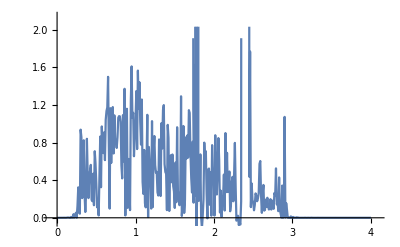

```mathematica
Module[{B1=Transpose[{m100[[1;;400]][[;;,1]],(m100[[1;;400,2]]-  Import["/home/shardulmukim/33imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
```

0.0281844

```mathematica
Module[{B1=Transpose[{m100[[1;;400]][[;;,1]],(m100[[1;;400,2]]-  Import["/home/shardulmukim/50imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
```

0.0267619

```mathematica
Module[{B1=Transpose[{m100[[1;;400]][[;;,1]],(m100[[1;;400,2]]-  Import["/home/shardulmukim/100imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
```

0.024432

```mathematica
Export["100imp7.csv",%170]
```

100imp7.csv

```mathematica
Table[{ω,Mean[Table[tr100[ω,0.001,t,0,0.7],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000160537},{0.01,0.000120873},{0.02,0.0000899181},{0.03,0.0000662334},{0.04,0.0000800389},{0.05,0.000107068},{0.06,0.000148715},{0.07,0.000222474},{0.08,0.000310212},{0.09,0.000424463},{0.1,0.000557215},{0.11,0.00075654},{0.12,0.000940037},{0.13,0.00117633},{0.14,0.00159514},{0.15,0.00199947},{0.16,0.00251249},{0.17,0.00325854},{0.18,0.00420557},{0.19,0.00576501},{0.2,0.00782301},{0.21,0.0101431},{0.22,0.0157502},{0.23,0.0283537},{0.24,0.0439349},{0.25,0.0529955},{0.26,0.070573},{0.27,0.141528},{0.28,0.304775},{0.29,0.400983},{0.3,0.435477},{0.31,0.448384},{0.32,0.461995},{0.33,0.458453},{0.34,0.45485},{0.35,0.457903},{0.36,0.443961},{0.37,0.444635},{0.38,0.438439},{0.39,0.429544},{0.4,0.42011},{0.41,0.451314},{0.42,0.508393},{0.43,0.537054},{0.44,0.536083},{0.45,0.563215},{0.46,0.589837},{0.47,0.576042},{0.48,0.582565},{0.49,0.566742},{0.5,0.570408},{0.51,0.588012},{0.52,0.591672},{0.53,0.603401},{0.54,0.630559},{0.55,0.646565},{0.56,0.654303},{0.57,0.658713},{0.58,0.687441},{0.59,0.698753},{0.6,0.721941},{0.61,0.740268},{0.62,0.746806},{0.63,0.765647},{0.64,0.76191},{0.65,0.783243},{0.66,0.770556},{0.67,0.802798},{0.68,0.811878},{0.69,0.809426},{0.7,0.832902},{0.71,0.82995},{0.72,0.838067},{0.73,0.829079},{0.74,0.852188},{0.75,0.86136},{0.76,0.8642},{0.77,0.867723},{0.78,0.872283},{0.79,0.868056},{0.8,0.871602},{0.81,0.854236},{0.82,0.839515},{0.83,0.8052},{0.84,0.738929},{0.85,0.687237},{0.86,0.693298},{0.87,0.709638},{0.88,0.68947},{0.89,0.687652},{0.9,0.661561},{0.91,0.683719},{0.92,0.739101},{0.93,0.735718},{0.94,0.786106},{0.95,0.848275},{0.96,0.911144},{0.97,0.947976},{0.98,0.988183},{0.99,1.06137},{1.,1.13382},{1.01,1.24065},{1.02,1.29144},{1.03,1.27738},{1.04,1.20454},{1.05,1.06737},{1.06,0.881833},{1.07,0.655177},{1.08,0.46716},{1.09,0.389162},{1.1,0.361681},{1.11,0.405609},{1.12,0.431254},{1.13,0.443911},{1.14,0.463511},{1.15,0.464241},{1.16,0.486553},{1.17,0.498397},{1.18,0.521044},{1.19,0.534994},{1.2,0.552167},{1.21,0.557892},{1.22,0.579634},{1.23,0.601821},{1.24,0.611283},{1.25,0.622142},{1.26,0.62804},{1.27,0.626604},{1.28,0.641858},{1.29,0.633701},{1.3,0.638724},{1.31,0.647399},{1.32,0.640237},{1.33,0.666059},{1.34,0.65104},{1.35,0.661772},{1.36,0.66015},{1.37,0.668473},{1.38,0.663041},{1.39,0.663631},{1.4,0.666666},{1.41,0.652165},{1.42,0.656563},{1.43,0.656618},{1.44,0.650946},{1.45,0.637858},{1.46,0.644214},{1.47,0.638059},{1.48,0.645696},{1.49,0.64679},{1.5,0.643062},{1.51,0.627908},{1.52,0.627354},{1.53,0.621555},{1.54,0.616422},{1.55,0.591944},{1.56,0.588697},{1.57,0.587062},{1.58,0.577603},{1.59,0.568569},{1.6,0.567661},{1.61,0.553591},{1.62,0.543335},{1.63,0.537168},{1.64,0.529109},{1.65,0.508352},{1.66,0.493541},{1.67,0.496659},{1.68,0.489738},{1.69,0.48775},{1.7,0.493412},{1.71,0.512184},{1.72,0.557611},{1.73,0.643713},{1.74,0.777331},{1.75,1.08341},{1.76,1.75443},{1.77,3.63284},{1.78,3.28174},{1.79,3.16797},{1.8,2.79961},{1.81,2.45112},{1.82,1.70476},{1.83,1.32934},{1.84,1.071},{1.85,0.665889},{1.86,0.521991},{1.87,0.444339},{1.88,0.413341},{1.89,0.419283},{1.9,0.427924},{1.91,0.4319},{1.92,0.441417},{1.93,0.463826},{1.94,0.482365},{1.95,0.489191},{1.96,0.499795},{1.97,0.502796},{1.98,0.506278},{1.99,0.52318},{2.,0.534195},{2.01,0.518196},{2.02,0.532988},{2.03,0.539803},{2.04,0.529096},{2.05,0.520262},{2.06,0.542046},{2.07,0.531231},{2.08,0.529691},{2.09,0.539298},{2.1,0.536178},{2.11,0.547591},{2.12,0.534061},{2.13,0.541401},{2.14,0.538644},{2.15,0.529958},{2.16,0.53882},{2.17,0.536664},{2.18,0.520115},{2.19,0.522804},{2.2,0.52439},{2.21,0.505474},{2.22,0.498356},{2.23,0.512469},{2.24,0.492857},{2.25,0.497367},{2.26,0.487433},{2.27,0.477839},{2.28,0.47665},{2.29,0.472388},{2.3,0.463437},{2.31,0.451895},{2.32,0.44371},{2.33,0.444673},{2.34,0.425074},{2.35,0.411389},{2.36,0.410277},{2.37,0.405192},{2.38,0.404463},{2.39,0.435576},{2.4,0.504408},{2.41,0.776768},{2.42,1.736},{2.43,1.71023},{2.44,1.74521},{2.45,1.6964},{2.46,1.31176},{2.47,0.952077},{2.48,0.711242},{2.49,0.545668},{2.5,0.419092},{2.51,0.339342},{2.52,0.317671},{2.53,0.284452},{2.54,0.269387},{2.55,0.246},{2.56,0.257937},{2.57,0.274619},{2.58,0.270836},{2.59,0.265418},{2.6,0.277663},{2.61,0.26296},{2.62,0.274462},{2.63,0.284597},{2.64,0.283042},{2.65,0.289641},{2.66,0.291145},{2.67,0.284841},{2.68,0.278849},{2.69,0.288241},{2.7,0.296412},{2.71,0.298275},{2.72,0.306144},{2.73,0.308087},{2.74,0.299347},{2.75,0.30092},{2.76,0.299034},{2.77,0.30068},{2.78,0.301831},{2.79,0.294062},{2.8,0.293842},{2.81,0.28631},{2.82,0.29492},{2.83,0.30108},{2.84,0.294663},{2.85,1.13543},{2.86,1.17025},{2.87,0.897163},{2.88,1.23915},{2.89,0.601},{2.9,0.538874},{2.91,0.207842},{2.92,0.115137},{2.93,0.0443147},{2.94,0.0209353},{2.95,0.0135978},{2.96,0.00872553},{2.97,0.00657457},{2.98,0.00515909},{2.99,0.00379397},{3.,0.00300717},{3.01,0.0026596},{3.02,0.00213395},{3.03,0.00187766},{3.04,0.00158152},{3.05,0.00135516},{3.06,0.00122416},{3.07,0.00101571},{3.08,0.000850228},{3.09,0.000802862},{3.1,0.000686309},{3.11,0.000565661},{3.12,0.000588514},{3.13,0.00049973},{3.14,0.000439802},{3.15,0.000444884},{3.16,0.00036445},{3.17,0.0003447},{3.18,0.000295892},{3.19,0.000272057},{3.2,0.000261281},{3.21,0.000217115},{3.22,0.000188414},{3.23,0.000191744},{3.24,0.000171336},{3.25,0.0001589},{3.26,0.000144163},{3.27,0.000133048},{3.28,0.000131808},{3.29,0.000113351},{3.3,0.000102839},{3.31,0.000102497},{3.32,0.0000938611},{3.33,0.0000876043},{3.34,0.000078199},{3.35,0.0000751967},{3.36,0.0000640305},{3.37,0.0000648572},{3.38,0.000060544},{3.39,0.0000603655},{3.4,0.0000511476},{3.41,0.0000468589},{3.42,0.0000483191},{3.43,0.0000437686},{3.44,0.0000455277},{3.45,0.0000407256},{3.46,0.0000349156},{3.47,0.000035479},{3.48,0.000033637},{3.49,0.0000299422},{3.5,0.0000277},{3.51,0.0000278279},{3.52,0.0000250664},{3.53,0.0000236424},{3.54,0.0000228892},{3.55,0.0000196531},{3.56,0.0000190878},{3.57,0.0000189093},{3.58,0.0000185443},{3.59,0.0000168555},{3.6,0.0000154164},{3.61,0.0000163983},{3.62,0.000015038},{3.63,0.0000128782},{3.64,0.0000129375},{3.65,0.0000122346},{3.66,0.0000126507},{3.67,0.0000113595},{3.68,0.0000105055},{3.69,9.51334×10^-6},{3.7,0.000011133},{3.71,9.95002×10^-6},{3.72,8.96274×10^-6},{3.73,8.46385×10^-6},{3.74,8.48266×10^-6},{3.75,8.10804×10^-6},{3.76,7.7469×10^-6},{3.77,6.98881×10^-6},{3.78,6.52429×10^-6},{3.79,6.37451×10^-6},{3.8,6.54883×10^-6},{3.81,5.86777×10^-6},{3.82,5.63982×10^-6},{3.83,5.57125×10^-6},{3.84,5.2282×10^-6},{3.85,5.22736×10^-6},{3.86,4.61752×10^-6},{3.87,4.68206×10^-6},{3.88,4.6004×10^-6},{3.89,4.32313×10^-6},{3.9,4.00263×10^-6},{3.91,4.00284×10^-6},{3.92,3.99294×10^-6},{3.93,3.78915×10^-6},{3.94,3.11498×10^-6},{3.95,3.45077×10^-6},{3.96,3.18469×10^-6},{3.97,3.06658×10^-6},{3.98,2.66608×10^-6},{3.99,2.75537×10^-6},{4.,2.48911×10^-6}}

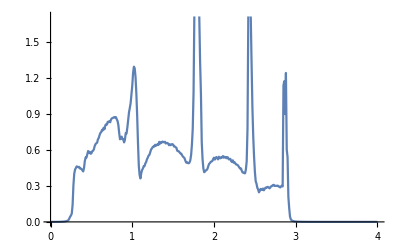

```mathematica
ListPlot[%170,Joined->True]
```

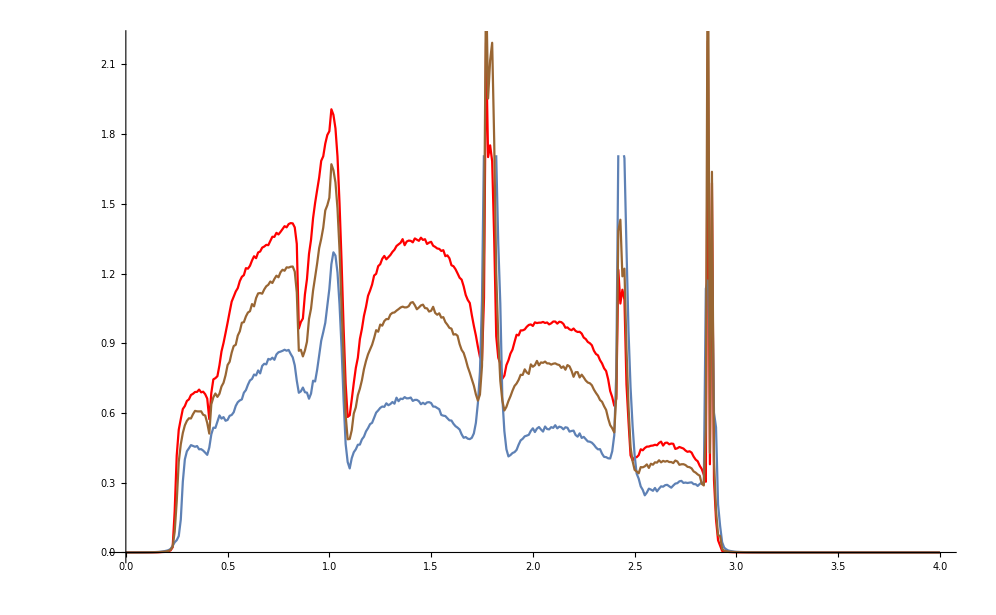

```mathematica
Show[%182,%174,%185]
```

```mathematica
tr33[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],T=},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{gg,gg,Inverse[Module[{i=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[i,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[T].J.T].c],100]; J=J]; Il1:=Inverse[IdentityMatrix[14]-sl1.TT[1].SR[ω,0.001,t,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];
η]
```

```mathematica
Export["33imp7.csv",%172]
```

33imp7.csv

```mathematica
Table[{ω,Mean[Table[tr33[ω,0.001,t,0,0.7],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000360234},{0.01,0.0000361636},{0.02,0.0000312348},{0.03,0.0000358793},{0.04,0.0000451749},{0.05,0.0000618323},{0.06,0.0000957944},{0.07,0.000130603},{0.08,0.000160627},{0.09,0.000221267},{0.1,0.000290352},{0.11,0.000340004},{0.12,0.000444028},{0.13,0.000624067},{0.14,0.000735753},{0.15,0.000929451},{0.16,0.00113806},{0.17,0.00164895},{0.18,0.00205972},{0.19,0.00247052},{0.2,0.00368362},{0.21,0.00555231},{0.22,0.0091529},{0.23,0.022415},{0.24,0.178164},{0.25,0.416985},{0.26,0.528361},{0.27,0.574108},{0.28,0.617311},{0.29,0.630101},{0.3,0.651885},{0.31,0.658829},{0.32,0.677571},{0.33,0.682851},{0.34,0.6905},{0.35,0.690996},{0.36,0.700906},{0.37,0.689031},{0.38,0.691818},{0.39,0.681041},{0.4,0.661949},{0.41,0.573705},{0.42,0.686333},{0.43,0.74499},{0.44,0.749988},{0.45,0.758558},{0.46,0.805637},{0.47,0.865092},{0.48,0.90145},{0.49,0.944512},{0.5,0.988589},{0.51,1.03475},{0.52,1.07924},{0.53,1.10081},{0.54,1.12285},{0.55,1.1374},{0.56,1.16764},{0.57,1.18606},{0.58,1.19344},{0.59,1.22332},{0.6,1.22113},{0.61,1.23372},{0.62,1.25635},{0.63,1.27448},{0.64,1.26638},{0.65,1.29084},{0.66,1.29489},{0.67,1.31164},{0.68,1.31627},{0.69,1.32359},{0.7,1.32221},{0.71,1.34051},{0.72,1.35844},{0.73,1.35791},{0.74,1.37538},{0.75,1.36832},{0.76,1.37936},{0.77,1.39146},{0.78,1.40395},{0.79,1.39894},{0.8,1.41297},{0.81,1.41717},{0.82,1.41598},{0.83,1.39871},{0.84,1.32766},{0.85,0.96364},{0.86,0.991674},{0.87,1.00672},{0.88,1.1106},{0.89,1.17606},{0.9,1.28478},{0.91,1.34549},{0.92,1.43858},{0.93,1.50383},{0.94,1.55927},{0.95,1.61345},{0.96,1.68504},{0.97,1.70474},{0.98,1.75933},{0.99,1.79622},{1.,1.81242},{1.01,1.90695},{1.02,1.8831},{1.03,1.8249},{1.04,1.70401},{1.05,1.50233},{1.06,1.2524},{1.07,0.967913},{1.08,0.72663},{1.09,0.583205},{1.1,0.59007},{1.11,0.657898},{1.12,0.72926},{1.13,0.793827},{1.14,0.837596},{1.15,0.918188},{1.16,0.962181},{1.17,1.01785},{1.18,1.05663},{1.19,1.10416},{1.2,1.12667},{1.21,1.15262},{1.22,1.19167},{1.23,1.19907},{1.24,1.23198},{1.25,1.24045},{1.26,1.26382},{1.27,1.27593},{1.28,1.26138},{1.29,1.27062},{1.3,1.27999},{1.31,1.29324},{1.32,1.30271},{1.33,1.31865},{1.34,1.32571},{1.35,1.33244},{1.36,1.34815},{1.37,1.32208},{1.38,1.33775},{1.39,1.34189},{1.4,1.34077},{1.41,1.33434},{1.42,1.35121},{1.43,1.34591},{1.44,1.34089},{1.45,1.35434},{1.46,1.34481},{1.47,1.3479},{1.48,1.32744},{1.49,1.33321},{1.5,1.33671},{1.51,1.31982},{1.52,1.31485},{1.53,1.30801},{1.54,1.3063},{1.55,1.2973},{1.56,1.3007},{1.57,1.27493},{1.58,1.27842},{1.59,1.26573},{1.6,1.23573},{1.61,1.23156},{1.62,1.21852},{1.63,1.20085},{1.64,1.18215},{1.65,1.17398},{1.66,1.14524},{1.67,1.10821},{1.68,1.08677},{1.69,1.07346},{1.7,1.02164},{1.71,0.975176},{1.72,0.933706},{1.73,0.88473},{1.74,0.840741},{1.75,0.825252},{1.76,1.09587},{1.77,2.19381},{1.78,1.70116},{1.79,1.75173},{1.8,1.68338},{1.81,1.35166},{1.82,0.930294},{1.83,0.8375},{1.84,0.814263},{1.85,0.747505},{1.86,0.76091},{1.87,0.806036},{1.88,0.827009},{1.89,0.855906},{1.9,0.873021},{1.91,0.905893},{1.92,0.9369},{1.93,0.934107},{1.94,0.955419},{1.95,0.955684},{1.96,0.959754},{1.97,0.971123},{1.98,0.979021},{1.99,0.981256},{2.,0.974681},{2.01,0.990122},{2.02,0.987094},{2.03,0.988823},{2.04,0.98881},{2.05,0.992001},{2.06,0.987475},{2.07,0.989641},{2.08,0.981343},{2.09,0.985979},{2.1,0.99365},{2.11,0.993641},{2.12,0.984646},{2.13,0.992796},{2.14,0.990986},{2.15,0.983546},{2.16,0.966948},{2.17,0.968346},{2.18,0.960175},{2.19,0.956455},{2.2,0.963593},{2.21,0.953162},{2.22,0.94876},{2.23,0.949579},{2.24,0.941733},{2.25,0.924611},{2.26,0.918215},{2.27,0.905744},{2.28,0.900443},{2.29,0.891465},{2.3,0.868064},{2.31,0.854089},{2.32,0.848122},{2.33,0.827534},{2.34,0.813344},{2.35,0.792551},{2.36,0.780702},{2.37,0.7452},{2.38,0.694489},{2.39,0.668451},{2.4,0.631239},{2.41,0.661212},{2.42,1.21613},{2.43,1.07116},{2.44,1.1306},{2.45,1.0875},{2.46,0.723376},{2.47,0.563393},{2.48,0.418048},{2.49,0.396585},{2.5,0.409541},{2.51,0.40994},{2.52,0.418585},{2.53,0.444084},{2.54,0.439724},{2.55,0.449458},{2.56,0.455438},{2.57,0.455826},{2.58,0.459227},{2.59,0.460123},{2.6,0.463468},{2.61,0.461314},{2.62,0.471356},{2.63,0.477003},{2.64,0.459932},{2.65,0.471611},{2.66,0.472723},{2.67,0.46547},{2.68,0.468679},{2.69,0.467517},{2.7,0.445556},{2.71,0.448473},{2.72,0.453907},{2.73,0.450617},{2.74,0.447164},{2.75,0.438704},{2.76,0.43308},{2.77,0.435554},{2.78,0.429709},{2.79,0.412535},{2.8,0.399689},{2.81,0.392377},{2.82,0.372983},{2.83,0.358941},{2.84,0.334036},{2.85,0.30433},{2.86,2.20072},{2.87,0.379556},{2.88,1.58945},{2.89,0.312493},{2.9,0.141551},{2.91,0.0526079},{2.92,0.0297909},{2.93,0.0070262},{2.94,0.00462713},{2.95,0.00323607},{2.96,0.00257879},{2.97,0.00186289},{2.98,0.00139715},{2.99,0.00127357},{3.,0.00106565},{3.01,0.000757277},{3.02,0.000672731},{3.03,0.000598732},{3.04,0.000491199},{3.05,0.000464133},{3.06,0.000384516},{3.07,0.000378243},{3.08,0.000296816},{3.09,0.000263982},{3.1,0.000233869},{3.11,0.00020449},{3.12,0.000181736},{3.13,0.000153225},{3.14,0.000171477},{3.15,0.000126582},{3.16,0.000125795},{3.17,0.000115389},{3.18,0.000102929},{3.19,0.0000829236},{3.2,0.0000892878},{3.21,0.0000702082},{3.22,0.0000674819},{3.23,0.0000645565},{3.24,0.0000536015},{3.25,0.0000511168},{3.26,0.0000509093},{3.27,0.0000499636},{3.28,0.0000419066},{3.29,0.000040847},{3.3,0.000034121},{3.31,0.0000371592},{3.32,0.0000294782},{3.33,0.0000270732},{3.34,0.0000263621},{3.35,0.000021564},{3.36,0.0000257438},{3.37,0.0000211445},{3.38,0.0000203919},{3.39,0.0000195946},{3.4,0.0000174519},{3.41,0.0000187928},{3.42,0.0000153786},{3.43,0.000017191},{3.44,0.0000170827},{3.45,0.0000146271},{3.46,0.0000135018},{3.47,0.0000118993},{3.48,0.0000111028},{3.49,0.0000102996},{3.5,8.41901×10^-6},{3.51,8.87476×10^-6},{3.52,9.52266×10^-6},{3.53,7.15542×10^-6},{3.54,6.69433×10^-6},{3.55,7.66848×10^-6},{3.56,7.62381×10^-6},{3.57,7.22649×10^-6},{3.58,6.06322×10^-6},{3.59,6.97815×10^-6},{3.6,6.45655×10^-6},{3.61,4.77419×10^-6},{3.62,5.30986×10^-6},{3.63,4.29506×10^-6},{3.64,4.68516×10^-6},{3.65,4.96563×10^-6},{3.66,3.95702×10^-6},{3.67,4.78722×10^-6},{3.68,3.49101×10^-6},{3.69,3.71637×10^-6},{3.7,3.19281×10^-6},{3.71,3.29835×10^-6},{3.72,3.12567×10^-6},{3.73,3.24636×10^-6},{3.74,2.64687×10^-6},{3.75,2.92842×10^-6},{3.76,2.50054×10^-6},{3.77,2.29684×10^-6},{3.78,2.44664×10^-6},{3.79,2.27196×10^-6},{3.8,2.4764×10^-6},{3.81,2.01179×10^-6},{3.82,2.1071×10^-6},{3.83,1.87621×10^-6},{3.84,1.71028×10^-6},{3.85,1.82119×10^-6},{3.86,1.69432×10^-6},{3.87,1.52157×10^-6},{3.88,1.5204×10^-6},{3.89,1.55593×10^-6},{3.9,1.38172×10^-6},{3.91,1.35318×10^-6},{3.92,1.38246×10^-6},{3.93,1.08911×10^-6},{3.94,1.20849×10^-6},{3.95,1.18941×10^-6},{3.96,1.1178×10^-6},{3.97,1.21541×10^-6},{3.98,1.02594×10^-6},{3.99,1.03971×10^-6},{4.,9.98317×10^-7}}

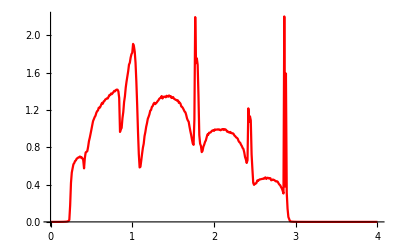

```mathematica
ListPlot[%172,Joined->True,PlotStyle->Red]
```

```mathematica
12/49
```

12/49

```mathematica
N[11/49]
```

0.22449

```mathematica
dataset33= Import["33imp7.csv"]
```

{{0.,0.0000360234},{0.01,0.0000361636},{0.02,0.0000312348},{0.03,0.0000358793},{0.04,0.0000451749},{0.05,0.0000618323},{0.06,0.0000957944},{0.07,0.000130603},{0.08,0.000160627},{0.09,0.000221267},{0.1,0.000290352},{0.11,0.000340004},{0.12,0.000444028},{0.13,0.000624067},{0.14,0.000735753},{0.15,0.000929451},{0.16,0.00113806},{0.17,0.00164895},{0.18,0.00205972},{0.19,0.00247052},{0.2,0.00368362},{0.21,0.00555231},{0.22,0.0091529},{0.23,0.022415},{0.24,0.178164},{0.25,0.416985},{0.26,0.528361},{0.27,0.574108},{0.28,0.617311},{0.29,0.630101},{0.3,0.651885},{0.31,0.658829},{0.32,0.677571},{0.33,0.682851},{0.34,0.6905},{0.35,0.690996},{0.36,0.700906},{0.37,0.689031},{0.38,0.691818},{0.39,0.681041},{0.4,0.661949},{0.41,0.573705},{0.42,0.686333},{0.43,0.74499},{0.44,0.749988},{0.45,0.758558},{0.46,0.805637},{0.47,0.865092},{0.48,0.90145},{0.49,0.944512},{0.5,0.988589},{0.51,1.03475},{0.52,1.07924},{0.53,1.10081},{0.54,1.12285},{0.55,1.1374},{0.56,1.16764},{0.57,1.18606},{0.58,1.19344},{0.59,1.22332},{0.6,1.22113},{0.61,1.23372},{0.62,1.25635},{0.63,1.27448},{0.64,1.26638},{0.65,1.29084},{0.66,1.29489},{0.67,1.31164},{0.68,1.31627},{0.69,1.32359},{0.7,1.32221},{0.71,1.34051},{0.72,1.35844},{0.73,1.35791},{0.74,1.37538},{0.75,1.36832},{0.76,1.37936},{0.77,1.39146},{0.78,1.40395},{0.79,1.39894},{0.8,1.41297},{0.81,1.41717},{0.82,1.41598},{0.83,1.39871},{0.84,1.32766},{0.85,0.96364},{0.86,0.991674},{0.87,1.00672},{0.88,1.1106},{0.89,1.17606},{0.9,1.28478},{0.91,1.34549},{0.92,1.43858},{0.93,1.50383},{0.94,1.55927},{0.95,1.61345},{0.96,1.68504},{0.97,1.70474},{0.98,1.75933},{0.99,1.79622},{1.,1.81242},{1.01,1.90695},{1.02,1.8831},{1.03,1.8249},{1.04,1.70401},{1.05,1.50233},{1.06,1.2524},{1.07,0.967913},{1.08,0.72663},{1.09,0.583205},{1.1,0.59007},{1.11,0.657898},{1.12,0.72926},{1.13,0.793827},{1.14,0.837596},{1.15,0.918188},{1.16,0.962181},{1.17,1.01785},{1.18,1.05663},{1.19,1.10416},{1.2,1.12667},{1.21,1.15262},{1.22,1.19167},{1.23,1.19907},{1.24,1.23198},{1.25,1.24045},{1.26,1.26382},{1.27,1.27593},{1.28,1.26138},{1.29,1.27062},{1.3,1.27999},{1.31,1.29324},{1.32,1.30271},{1.33,1.31865},{1.34,1.32571},{1.35,1.33244},{1.36,1.34815},{1.37,1.32208},{1.38,1.33775},{1.39,1.34189},{1.4,1.34077},{1.41,1.33434},{1.42,1.35121},{1.43,1.34591},{1.44,1.34089},{1.45,1.35434},{1.46,1.34481},{1.47,1.3479},{1.48,1.32744},{1.49,1.33321},{1.5,1.33671},{1.51,1.31982},{1.52,1.31485},{1.53,1.30801},{1.54,1.3063},{1.55,1.2973},{1.56,1.3007},{1.57,1.27493},{1.58,1.27842},{1.59,1.26573},{1.6,1.23573},{1.61,1.23156},{1.62,1.21852},{1.63,1.20085},{1.64,1.18215},{1.65,1.17398},{1.66,1.14524},{1.67,1.10821},{1.68,1.08677},{1.69,1.07346},{1.7,1.02164},{1.71,0.975176},{1.72,0.933706},{1.73,0.88473},{1.74,0.840741},{1.75,0.825252},{1.76,1.09587},{1.77,2.19381},{1.78,1.70116},{1.79,1.75173},{1.8,1.68338},{1.81,1.35166},{1.82,0.930294},{1.83,0.8375},{1.84,0.814263},{1.85,0.747505},{1.86,0.76091},{1.87,0.806036},{1.88,0.827009},{1.89,0.855906},{1.9,0.873021},{1.91,0.905893},{1.92,0.9369},{1.93,0.934107},{1.94,0.955419},{1.95,0.955684},{1.96,0.959754},{1.97,0.971123},{1.98,0.979021},{1.99,0.981256},{2.,0.974681},{2.01,0.990122},{2.02,0.987094},{2.03,0.988823},{2.04,0.98881},{2.05,0.992001},{2.06,0.987475},{2.07,0.989641},{2.08,0.981343},{2.09,0.985979},{2.1,0.99365},{2.11,0.993641},{2.12,0.984646},{2.13,0.992796},{2.14,0.990986},{2.15,0.983546},{2.16,0.966948},{2.17,0.968346},{2.18,0.960175},{2.19,0.956455},{2.2,0.963593},{2.21,0.953162},{2.22,0.94876},{2.23,0.949579},{2.24,0.941733},{2.25,0.924611},{2.26,0.918215},{2.27,0.905744},{2.28,0.900443},{2.29,0.891465},{2.3,0.868064},{2.31,0.854089},{2.32,0.848122},{2.33,0.827534},{2.34,0.813344},{2.35,0.792551},{2.36,0.780702},{2.37,0.7452},{2.38,0.694489},{2.39,0.668451},{2.4,0.631239},{2.41,0.661212},{2.42,1.21613},{2.43,1.07116},{2.44,1.1306},{2.45,1.0875},{2.46,0.723376},{2.47,0.563393},{2.48,0.418048},{2.49,0.396585},{2.5,0.409541},{2.51,0.40994},{2.52,0.418585},{2.53,0.444084},{2.54,0.439724},{2.55,0.449458},{2.56,0.455438},{2.57,0.455826},{2.58,0.459227},{2.59,0.460123},{2.6,0.463468},{2.61,0.461314},{2.62,0.471356},{2.63,0.477003},{2.64,0.459932},{2.65,0.471611},{2.66,0.472723},{2.67,0.46547},{2.68,0.468679},{2.69,0.467517},{2.7,0.445556},{2.71,0.448473},{2.72,0.453907},{2.73,0.450617},{2.74,0.447164},{2.75,0.438704},{2.76,0.43308},{2.77,0.435554},{2.78,0.429709},{2.79,0.412535},{2.8,0.399689},{2.81,0.392377},{2.82,0.372983},{2.83,0.358941},{2.84,0.334036},{2.85,0.30433},{2.86,2.20072},{2.87,0.379556},{2.88,1.58945},{2.89,0.312493},{2.9,0.141551},{2.91,0.0526079},{2.92,0.0297909},{2.93,0.0070262},{2.94,0.00462713},{2.95,0.00323607},{2.96,0.00257879},{2.97,0.00186289},{2.98,0.00139715},{2.99,0.00127357},{3.,0.00106565},{3.01,0.000757277},{3.02,0.000672731},{3.03,0.000598732},{3.04,0.000491199},{3.05,0.000464133},{3.06,0.000384516},{3.07,0.000378243},{3.08,0.000296816},{3.09,0.000263982},{3.1,0.000233869},{3.11,0.00020449},{3.12,0.000181736},{3.13,0.000153225},{3.14,0.000171477},{3.15,0.000126582},{3.16,0.000125795},{3.17,0.000115389},{3.18,0.000102929},{3.19,0.0000829236},{3.2,0.0000892878},{3.21,0.0000702082},{3.22,0.0000674819},{3.23,0.0000645565},{3.24,0.0000536015},{3.25,0.0000511168},{3.26,0.0000509093},{3.27,0.0000499636},{3.28,0.0000419066},{3.29,0.000040847},{3.3,0.000034121},{3.31,0.0000371592},{3.32,0.0000294782},{3.33,0.0000270732},{3.34,0.0000263621},{3.35,0.000021564},{3.36,0.0000257438},{3.37,0.0000211445},{3.38,0.0000203919},{3.39,0.0000195946},{3.4,0.0000174519},{3.41,0.0000187928},{3.42,0.0000153786},{3.43,0.000017191},{3.44,0.0000170827},{3.45,0.0000146271},{3.46,0.0000135018},{3.47,0.0000118993},{3.48,0.0000111028},{3.49,0.0000102996},{3.5,8.41901×10^-6},{3.51,8.87476×10^-6},{3.52,9.52266×10^-6},{3.53,7.15542×10^-6},{3.54,6.69433×10^-6},{3.55,7.66848×10^-6},{3.56,7.62381×10^-6},{3.57,7.22649×10^-6},{3.58,6.06322×10^-6},{3.59,6.97815×10^-6},{3.6,6.45655×10^-6},{3.61,4.77419×10^-6},{3.62,5.30986×10^-6},{3.63,4.29506×10^-6},{3.64,4.68516×10^-6},{3.65,4.96563×10^-6},{3.66,3.95702×10^-6},{3.67,4.78722×10^-6},{3.68,3.49101×10^-6},{3.69,3.71637×10^-6},{3.7,3.19281×10^-6},{3.71,3.29835×10^-6},{3.72,3.12567×10^-6},{3.73,3.24636×10^-6},{3.74,2.64687×10^-6},{3.75,2.92842×10^-6},{3.76,2.50054×10^-6},{3.77,2.29684×10^-6},{3.78,2.44664×10^-6},{3.79,2.27196×10^-6},{3.8,2.4764×10^-6},{3.81,2.01179×10^-6},{3.82,2.1071×10^-6},{3.83,1.87621×10^-6},{3.84,1.71028×10^-6},{3.85,1.82119×10^-6},{3.86,1.69432×10^-6},{3.87,1.52157×10^-6},{3.88,1.5204×10^-6},{3.89,1.55593×10^-6},{3.9,1.38172×10^-6},{3.91,1.35318×10^-6},{3.92,1.38246×10^-6},{3.93,1.08911×10^-6},{3.94,1.20849×10^-6},{3.95,1.18941×10^-6},{3.96,1.1178×10^-6},{3.97,1.21541×10^-6},{3.98,1.02594×10^-6},{3.99,1.03971×10^-6},{4.,9.98317×10^-7}}

```mathematica
dataset50=Import["50imp7.csv"]
```

{{0.,0.0000546916},{0.01,0.0000438348},{0.02,0.0000385163},{0.03,0.0000401327},{0.04,0.0000528631},{0.05,0.0000750199},{0.06,0.00011624},{0.07,0.000155039},{0.08,0.000215326},{0.09,0.000286202},{0.1,0.000368295},{0.11,0.000467509},{0.12,0.000615624},{0.13,0.000765239},{0.14,0.00100828},{0.15,0.00124047},{0.16,0.00161473},{0.17,0.00210356},{0.18,0.00278342},{0.19,0.00371369},{0.2,0.0049719},{0.21,0.00736976},{0.22,0.0119294},{0.23,0.0251129},{0.24,0.0892294},{0.25,0.219381},{0.26,0.390204},{0.27,0.465354},{0.28,0.514168},{0.29,0.547117},{0.3,0.566322},{0.31,0.577421},{0.32,0.576707},{0.33,0.595039},{0.34,0.609285},{0.35,0.607234},{0.36,0.606839},{0.37,0.607411},{0.38,0.592531},{0.39,0.589231},{0.4,0.556913},{0.41,0.511479},{0.42,0.637298},{0.43,0.667602},{0.44,0.683966},{0.45,0.669505},{0.46,0.682918},{0.47,0.714196},{0.48,0.730206},{0.49,0.762654},{0.5,0.806662},{0.51,0.820588},{0.52,0.859546},{0.53,0.888161},{0.54,0.893545},{0.55,0.933305},{0.56,0.951595},{0.57,0.988427},{0.58,0.991199},{0.59,1.01564},{0.6,1.03242},{0.61,1.03818},{0.62,1.06877},{0.63,1.05908},{0.64,1.09459},{0.65,1.11468},{0.66,1.11625},{0.67,1.11351},{0.68,1.13176},{0.69,1.14538},{0.7,1.15182},{0.71,1.16594},{0.72,1.1594},{0.73,1.17688},{0.74,1.19092},{0.75,1.18406},{0.76,1.20579},{0.77,1.21653},{0.78,1.21217},{0.79,1.22684},{0.8,1.22576},{0.81,1.22946},{0.82,1.23037},{0.83,1.20863},{0.84,1.11882},{0.85,0.867765},{0.86,0.872174},{0.87,0.84363},{0.88,0.86908},{0.89,0.906847},{0.9,1.00474},{0.91,1.0491},{0.92,1.12706},{0.93,1.18455},{0.94,1.24349},{0.95,1.30998},{0.96,1.34926},{0.97,1.39747},{0.98,1.47179},{0.99,1.49389},{1.,1.52605},{1.01,1.6704},{1.02,1.64499},{1.03,1.59218},{1.04,1.4803},{1.05,1.3023},{1.06,1.05861},{1.07,0.836672},{1.08,0.591782},{1.09,0.487103},{1.1,0.488414},{1.11,0.525741},{1.12,0.59777},{1.13,0.624481},{1.14,0.676889},{1.15,0.70473},{1.16,0.741047},{1.17,0.788605},{1.18,0.823774},{1.19,0.85235},{1.2,0.873164},{1.21,0.8936},{1.22,0.92252},{1.23,0.956392},{1.24,0.949947},{1.25,0.98077},{1.26,0.975865},{1.27,0.995668},{1.28,1.00436},{1.29,1.00415},{1.3,1.024},{1.31,1.03111},{1.32,1.03279},{1.33,1.04055},{1.34,1.04692},{1.35,1.05401},{1.36,1.0578},{1.37,1.0544},{1.38,1.05479},{1.39,1.05971},{1.4,1.07453},{1.41,1.07725},{1.42,1.06394},{1.43,1.0465},{1.44,1.05408},{1.45,1.06303},{1.46,1.06628},{1.47,1.05147},{1.48,1.05056},{1.49,1.0366},{1.5,1.03975},{1.51,1.05703},{1.52,1.03082},{1.53,1.02283},{1.54,1.02926},{1.55,1.01052},{1.56,1.01251},{1.57,0.991167},{1.58,0.979863},{1.59,0.966319},{1.6,0.963215},{1.61,0.937518},{1.62,0.939398},{1.63,0.932361},{1.64,0.89663},{1.65,0.871709},{1.66,0.858652},{1.67,0.831273},{1.68,0.798509},{1.69,0.773554},{1.7,0.745456},{1.71,0.718071},{1.72,0.680524},{1.73,0.653364},{1.74,0.679312},{1.75,0.801729},{1.76,1.31103},{1.77,2.46673},{1.78,1.95339},{1.79,2.11635},{1.8,2.19303},{1.81,1.77276},{1.82,1.19926},{1.83,0.923784},{1.84,0.738682},{1.85,0.654093},{1.86,0.611066},{1.87,0.626551},{1.88,0.651878},{1.89,0.67226},{1.9,0.696275},{1.91,0.716501},{1.92,0.726958},{1.93,0.742587},{1.94,0.764531},{1.95,0.763945},{1.96,0.787967},{1.97,0.774649},{1.98,0.768221},{1.99,0.809368},{2.,0.799162},{2.01,0.806089},{2.02,0.824294},{2.03,0.805311},{2.04,0.817694},{2.05,0.815996},{2.06,0.821414},{2.07,0.813497},{2.08,0.81353},{2.09,0.80839},{2.1,0.812196},{2.11,0.813807},{2.12,0.808955},{2.13,0.806643},{2.14,0.794095},{2.15,0.800765},{2.16,0.786456},{2.17,0.806334},{2.18,0.800929},{2.19,0.782016},{2.2,0.755893},{2.21,0.775602},{2.22,0.775952},{2.23,0.753071},{2.24,0.765019},{2.25,0.753136},{2.26,0.739695},{2.27,0.731195},{2.28,0.728169},{2.29,0.719371},{2.3,0.700792},{2.31,0.686533},{2.32,0.674141},{2.33,0.656168},{2.34,0.648332},{2.35,0.629347},{2.36,0.613336},{2.37,0.576804},{2.38,0.547862},{2.39,0.534421},{2.4,0.516472},{2.41,0.679464},{2.42,1.3839},{2.43,1.43172},{2.44,1.18821},{2.45,1.22116},{2.46,0.876651},{2.47,0.62801},{2.48,0.452695},{2.49,0.393555},{2.5,0.355595},{2.51,0.348415},{2.52,0.340692},{2.53,0.367345},{2.54,0.3664},{2.55,0.370696},{2.56,0.379052},{2.57,0.363863},{2.58,0.381842},{2.59,0.37769},{2.6,0.387922},{2.61,0.386658},{2.62,0.396843},{2.63,0.387805},{2.64,0.394127},{2.65,0.390811},{2.66,0.394016},{2.67,0.389183},{2.68,0.389165},{2.69,0.384751},{2.7,0.395706},{2.71,0.391494},{2.72,0.37733},{2.73,0.379578},{2.74,0.379862},{2.75,0.376281},{2.76,0.368631},{2.77,0.367069},{2.78,0.361851},{2.79,0.348879},{2.8,0.343641},{2.81,0.335802},{2.82,0.330538},{2.83,0.295172},{2.84,0.288482},{2.85,0.531208},{2.86,2.89504},{2.87,0.428563},{2.88,1.63802},{2.89,0.397408},{2.9,0.180711},{2.91,0.0753806},{2.92,0.0705932},{2.93,0.0156212},{2.94,0.00800968},{2.95,0.00586348},{2.96,0.00394493},{2.97,0.00290064},{2.98,0.00237685},{2.99,0.00178249},{3.,0.00165015},{3.01,0.00116195},{3.02,0.00111529},{3.03,0.000918226},{3.04,0.000850781},{3.05,0.000695865},{3.06,0.000604391},{3.07,0.000491934},{3.08,0.00045379},{3.09,0.000391631},{3.1,0.000383974},{3.11,0.000345109},{3.12,0.000284303},{3.13,0.000263014},{3.14,0.000232381},{3.15,0.000204104},{3.16,0.000180205},{3.17,0.000162649},{3.18,0.000154127},{3.19,0.000140912},{3.2,0.000137839},{3.21,0.0000941593},{3.22,0.000101668},{3.23,0.0000992979},{3.24,0.0000966304},{3.25,0.0000805822},{3.26,0.0000739955},{3.27,0.0000704549},{3.28,0.0000631881},{3.29,0.0000586746},{3.3,0.0000534756},{3.31,0.0000511781},{3.32,0.0000456395},{3.33,0.0000459856},{3.34,0.0000378711},{3.35,0.0000376541},{3.36,0.0000376483},{3.37,0.0000345874},{3.38,0.0000314692},{3.39,0.0000261525},{3.4,0.0000246338},{3.41,0.0000265418},{3.42,0.0000240179},{3.43,0.0000225938},{3.44,0.0000197341},{3.45,0.0000214298},{3.46,0.0000176154},{3.47,0.0000172171},{3.48,0.000017526},{3.49,0.0000153632},{3.5,0.0000140934},{3.51,0.0000133848},{3.52,0.0000135026},{3.53,0.0000119456},{3.54,0.0000103173},{3.55,0.0000115808},{3.56,9.89222×10^-6},{3.57,9.30287×10^-6},{3.58,9.0141×10^-6},{3.59,9.71746×10^-6},{3.6,8.23758×10^-6},{3.61,8.02613×10^-6},{3.62,8.42807×10^-6},{3.63,7.10555×10^-6},{3.64,6.70781×10^-6},{3.65,6.10285×10^-6},{3.66,6.37681×10^-6},{3.67,6.47371×10^-6},{3.68,6.29599×10^-6},{3.69,5.88283×10^-6},{3.7,4.47169×10^-6},{3.71,5.15352×10^-6},{3.72,4.57496×10^-6},{3.73,4.36095×10^-6},{3.74,4.32289×10^-6},{3.75,4.17211×10^-6},{3.76,3.64761×10^-6},{3.77,3.55237×10^-6},{3.78,3.47376×10^-6},{3.79,3.41001×10^-6},{3.8,3.2063×10^-6},{3.81,3.34605×10^-6},{3.82,3.0306×10^-6},{3.83,2.63738×10^-6},{3.84,2.69155×10^-6},{3.85,2.73361×10^-6},{3.86,2.19788×10^-6},{3.87,2.43411×10^-6},{3.88,2.13457×10^-6},{3.89,2.0912×10^-6},{3.9,2.24552×10^-6},{3.91,1.98767×10^-6},{3.92,1.8982×10^-6},{3.93,1.85256×10^-6},{3.94,1.79495×10^-6},{3.95,1.89823×10^-6},{3.96,1.66484×10^-6},{3.97,1.63804×10^-6},{3.98,1.69342×10^-6},{3.99,1.49753×10^-6},{4.,1.46064×10^-6}}

```mathematica
dataset100=Import["100imp7.csv"]
```

{{0.,0.000160537},{0.01,0.000120873},{0.02,0.0000899181},{0.03,0.0000662334},{0.04,0.0000800389},{0.05,0.000107068},{0.06,0.000148715},{0.07,0.000222474},{0.08,0.000310212},{0.09,0.000424463},{0.1,0.000557215},{0.11,0.00075654},{0.12,0.000940037},{0.13,0.00117633},{0.14,0.00159514},{0.15,0.00199947},{0.16,0.00251249},{0.17,0.00325854},{0.18,0.00420557},{0.19,0.00576501},{0.2,0.00782301},{0.21,0.0101431},{0.22,0.0157502},{0.23,0.0283537},{0.24,0.0439349},{0.25,0.0529955},{0.26,0.070573},{0.27,0.141528},{0.28,0.304775},{0.29,0.400983},{0.3,0.435477},{0.31,0.448384},{0.32,0.461995},{0.33,0.458453},{0.34,0.45485},{0.35,0.457903},{0.36,0.443961},{0.37,0.444635},{0.38,0.438439},{0.39,0.429544},{0.4,0.42011},{0.41,0.451314},{0.42,0.508393},{0.43,0.537054},{0.44,0.536083},{0.45,0.563215},{0.46,0.589837},{0.47,0.576042},{0.48,0.582565},{0.49,0.566742},{0.5,0.570408},{0.51,0.588012},{0.52,0.591672},{0.53,0.603401},{0.54,0.630559},{0.55,0.646565},{0.56,0.654303},{0.57,0.658713},{0.58,0.687441},{0.59,0.698753},{0.6,0.721941},{0.61,0.740268},{0.62,0.746806},{0.63,0.765647},{0.64,0.76191},{0.65,0.783243},{0.66,0.770556},{0.67,0.802798},{0.68,0.811878},{0.69,0.809426},{0.7,0.832902},{0.71,0.82995},{0.72,0.838067},{0.73,0.829079},{0.74,0.852188},{0.75,0.86136},{0.76,0.8642},{0.77,0.867723},{0.78,0.872283},{0.79,0.868056},{0.8,0.871602},{0.81,0.854236},{0.82,0.839515},{0.83,0.8052},{0.84,0.738929},{0.85,0.687237},{0.86,0.693298},{0.87,0.709638},{0.88,0.68947},{0.89,0.687652},{0.9,0.661561},{0.91,0.683719},{0.92,0.739101},{0.93,0.735718},{0.94,0.786106},{0.95,0.848275},{0.96,0.911144},{0.97,0.947976},{0.98,0.988183},{0.99,1.06137},{1.,1.13382},{1.01,1.24065},{1.02,1.29144},{1.03,1.27738},{1.04,1.20454},{1.05,1.06737},{1.06,0.881833},{1.07,0.655177},{1.08,0.46716},{1.09,0.389162},{1.1,0.361681},{1.11,0.405609},{1.12,0.431254},{1.13,0.443911},{1.14,0.463511},{1.15,0.464241},{1.16,0.486553},{1.17,0.498397},{1.18,0.521044},{1.19,0.534994},{1.2,0.552167},{1.21,0.557892},{1.22,0.579634},{1.23,0.601821},{1.24,0.611283},{1.25,0.622142},{1.26,0.62804},{1.27,0.626604},{1.28,0.641858},{1.29,0.633701},{1.3,0.638724},{1.31,0.647399},{1.32,0.640237},{1.33,0.666059},{1.34,0.65104},{1.35,0.661772},{1.36,0.66015},{1.37,0.668473},{1.38,0.663041},{1.39,0.663631},{1.4,0.666666},{1.41,0.652165},{1.42,0.656563},{1.43,0.656618},{1.44,0.650946},{1.45,0.637858},{1.46,0.644214},{1.47,0.638059},{1.48,0.645696},{1.49,0.64679},{1.5,0.643062},{1.51,0.627908},{1.52,0.627354},{1.53,0.621555},{1.54,0.616422},{1.55,0.591944},{1.56,0.588697},{1.57,0.587062},{1.58,0.577603},{1.59,0.568569},{1.6,0.567661},{1.61,0.553591},{1.62,0.543335},{1.63,0.537168},{1.64,0.529109},{1.65,0.508352},{1.66,0.493541},{1.67,0.496659},{1.68,0.489738},{1.69,0.48775},{1.7,0.493412},{1.71,0.512184},{1.72,0.557611},{1.73,0.643713},{1.74,0.777331},{1.75,1.08341},{1.76,1.75443},{1.77,3.63284},{1.78,3.28174},{1.79,3.16797},{1.8,2.79961},{1.81,2.45112},{1.82,1.70476},{1.83,1.32934},{1.84,1.071},{1.85,0.665889},{1.86,0.521991},{1.87,0.444339},{1.88,0.413341},{1.89,0.419283},{1.9,0.427924},{1.91,0.4319},{1.92,0.441417},{1.93,0.463826},{1.94,0.482365},{1.95,0.489191},{1.96,0.499795},{1.97,0.502796},{1.98,0.506278},{1.99,0.52318},{2.,0.534195},{2.01,0.518196},{2.02,0.532988},{2.03,0.539803},{2.04,0.529096},{2.05,0.520262},{2.06,0.542046},{2.07,0.531231},{2.08,0.529691},{2.09,0.539298},{2.1,0.536178},{2.11,0.547591},{2.12,0.534061},{2.13,0.541401},{2.14,0.538644},{2.15,0.529958},{2.16,0.53882},{2.17,0.536664},{2.18,0.520115},{2.19,0.522804},{2.2,0.52439},{2.21,0.505474},{2.22,0.498356},{2.23,0.512469},{2.24,0.492857},{2.25,0.497367},{2.26,0.487433},{2.27,0.477839},{2.28,0.47665},{2.29,0.472388},{2.3,0.463437},{2.31,0.451895},{2.32,0.44371},{2.33,0.444673},{2.34,0.425074},{2.35,0.411389},{2.36,0.410277},{2.37,0.405192},{2.38,0.404463},{2.39,0.435576},{2.4,0.504408},{2.41,0.776768},{2.42,1.736},{2.43,1.71023},{2.44,1.74521},{2.45,1.6964},{2.46,1.31176},{2.47,0.952077},{2.48,0.711242},{2.49,0.545668},{2.5,0.419092},{2.51,0.339342},{2.52,0.317671},{2.53,0.284452},{2.54,0.269387},{2.55,0.246},{2.56,0.257937},{2.57,0.274619},{2.58,0.270836},{2.59,0.265418},{2.6,0.277663},{2.61,0.26296},{2.62,0.274462},{2.63,0.284597},{2.64,0.283042},{2.65,0.289641},{2.66,0.291145},{2.67,0.284841},{2.68,0.278849},{2.69,0.288241},{2.7,0.296412},{2.71,0.298275},{2.72,0.306144},{2.73,0.308087},{2.74,0.299347},{2.75,0.30092},{2.76,0.299034},{2.77,0.30068},{2.78,0.301831},{2.79,0.294062},{2.8,0.293842},{2.81,0.28631},{2.82,0.29492},{2.83,0.30108},{2.84,0.294663},{2.85,1.13543},{2.86,1.17025},{2.87,0.897163},{2.88,1.23915},{2.89,0.601},{2.9,0.538874},{2.91,0.207842},{2.92,0.115137},{2.93,0.0443147},{2.94,0.0209353},{2.95,0.0135978},{2.96,0.00872553},{2.97,0.00657457},{2.98,0.00515909},{2.99,0.00379397},{3.,0.00300717},{3.01,0.0026596},{3.02,0.00213395},{3.03,0.00187766},{3.04,0.00158152},{3.05,0.00135516},{3.06,0.00122416},{3.07,0.00101571},{3.08,0.000850228},{3.09,0.000802862},{3.1,0.000686309},{3.11,0.000565661},{3.12,0.000588514},{3.13,0.00049973},{3.14,0.000439802},{3.15,0.000444884},{3.16,0.00036445},{3.17,0.0003447},{3.18,0.000295892},{3.19,0.000272057},{3.2,0.000261281},{3.21,0.000217115},{3.22,0.000188414},{3.23,0.000191744},{3.24,0.000171336},{3.25,0.0001589},{3.26,0.000144163},{3.27,0.000133048},{3.28,0.000131808},{3.29,0.000113351},{3.3,0.000102839},{3.31,0.000102497},{3.32,0.0000938611},{3.33,0.0000876043},{3.34,0.000078199},{3.35,0.0000751967},{3.36,0.0000640305},{3.37,0.0000648572},{3.38,0.000060544},{3.39,0.0000603655},{3.4,0.0000511476},{3.41,0.0000468589},{3.42,0.0000483191},{3.43,0.0000437686},{3.44,0.0000455277},{3.45,0.0000407256},{3.46,0.0000349156},{3.47,0.000035479},{3.48,0.000033637},{3.49,0.0000299422},{3.5,0.0000277},{3.51,0.0000278279},{3.52,0.0000250664},{3.53,0.0000236424},{3.54,0.0000228892},{3.55,0.0000196531},{3.56,0.0000190878},{3.57,0.0000189093},{3.58,0.0000185443},{3.59,0.0000168555},{3.6,0.0000154164},{3.61,0.0000163983},{3.62,0.000015038},{3.63,0.0000128782},{3.64,0.0000129375},{3.65,0.0000122346},{3.66,0.0000126507},{3.67,0.0000113595},{3.68,0.0000105055},{3.69,9.51334×10^-6},{3.7,0.000011133},{3.71,9.95002×10^-6},{3.72,8.96274×10^-6},{3.73,8.46385×10^-6},{3.74,8.48266×10^-6},{3.75,8.10804×10^-6},{3.76,7.7469×10^-6},{3.77,6.98881×10^-6},{3.78,6.52429×10^-6},{3.79,6.37451×10^-6},{3.8,6.54883×10^-6},{3.81,5.86777×10^-6},{3.82,5.63982×10^-6},{3.83,5.57125×10^-6},{3.84,5.2282×10^-6},{3.85,5.22736×10^-6},{3.86,4.61752×10^-6},{3.87,4.68206×10^-6},{3.88,4.6004×10^-6},{3.89,4.32313×10^-6},{3.9,4.00263×10^-6},{3.91,4.00284×10^-6},{3.92,3.99294×10^-6},{3.93,3.78915×10^-6},{3.94,3.11498×10^-6},{3.95,3.45077×10^-6},{3.96,3.18469×10^-6},{3.97,3.06658×10^-6},{3.98,2.66608×10^-6},{3.99,2.75537×10^-6},{4.,2.48911×10^-6}}

```mathematica
Clear[trainingset]
```

```mathematica
Flatten[dataset33]
```

{0.,0.0000360234,0.01,0.0000361636,0.02,0.0000312348,0.03,0.0000358793,0.04,0.0000451749,0.05,0.0000618323,0.06,0.0000957944,0.07,0.000130603,0.08,0.000160627,0.09,0.000221267,0.1,0.000290352,0.11,0.000340004,0.12,0.000444028,0.13,0.000624067,0.14,0.000735753,0.15,0.000929451,0.16,0.00113806,0.17,0.00164895,0.18,0.00205972,0.19,0.00247052,0.2,0.00368362,0.21,0.00555231,0.22,0.0091529,0.23,0.022415,0.24,0.178164,0.25,0.416985,0.26,0.528361,0.27,0.574108,0.28,0.617311,0.29,0.630101,0.3,0.651885,0.31,0.658829,0.32,0.677571,0.33,0.682851,0.34,0.6905,0.35,0.690996,0.36,0.700906,0.37,0.689031,0.38,0.691818,0.39,0.681041,0.4,0.661949,0.41,0.573705,0.42,0.686333,0.43,0.74499,0.44,0.749988,0.45,0.758558,0.46,0.805637,0.47,0.865092,0.48,0.90145,0.49,0.944512,0.5,0.988589,0.51,1.03475,0.52,1.07924,0.53,1.10081,0.54,1.12285,0.55,1.1374,0.56,1.16764,0.57,1.18606,0.58,1.19344,0.59,1.22332,0.6,1.22113,0.61,1.23372,0.62,1.25635,0.63,1.27448,0.64,1.26638,0.65,1.29084,0.66,1.29489,0.67,1.31164,0.68,1.31627,0.69,1.32359,0.7,1.32221,0.71,1.34051,0.72,1.35844,0.73,1.35791,0.74,1.37538,0.75,1.36832,0.76,1.37936,0.77,1.39146,0.78,1.40395,0.79,1.39894,0.8,1.41297,0.81,1.41717,0.82,1.41598,0.83,1.39871,0.84,1.32766,0.85,0.96364,0.86,0.991674,0.87,1.00672,0.88,1.1106,0.89,1.17606,0.9,1.28478,0.91,1.34549,0.92,1.43858,0.93,1.50383,0.94,1.55927,0.95,1.61345,0.96,1.68504,0.97,1.70474,0.98,1.75933,0.99,1.79622,1.,1.81242,1.01,1.90695,1.02,1.8831,1.03,1.8249,1.04,1.70401,1.05,1.50233,1.06,1.2524,1.07,0.967913,1.08,0.72663,1.09,0.583205,1.1,0.59007,1.11,0.657898,1.12,0.72926,1.13,0.793827,1.14,0.837596,1.15,0.918188,1.16,0.962181,1.17,1.01785,1.18,1.05663,1.19,1.10416,1.2,1.12667,1.21,1.15262,1.22,1.19167,1.23,1.19907,1.24,1.23198,1.25,1.24045,1.26,1.26382,1.27,1.27593,1.28,1.26138,1.29,1.27062,1.3,1.27999,1.31,1.29324,1.32,1.30271,1.33,1.31865,1.34,1.32571,1.35,1.33244,1.36,1.34815,1.37,1.32208,1.38,1.33775,1.39,1.34189,1.4,1.34077,1.41,1.33434,1.42,1.35121,1.43,1.34591,1.44,1.34089,1.45,1.35434,1.46,1.34481,1.47,1.3479,1.48,1.32744,1.49,1.33321,1.5,1.33671,1.51,1.31982,1.52,1.31485,1.53,1.30801,1.54,1.3063,1.55,1.2973,1.56,1.3007,1.57,1.27493,1.58,1.27842,1.59,1.26573,1.6,1.23573,1.61,1.23156,1.62,1.21852,1.63,1.20085,1.64,1.18215,1.65,1.17398,1.66,1.14524,1.67,1.10821,1.68,1.08677,1.69,1.07346,1.7,1.02164,1.71,0.975176,1.72,0.933706,1.73,0.88473,1.74,0.840741,1.75,0.825252,1.76,1.09587,1.77,2.19381,1.78,1.70116,1.79,1.75173,1.8,1.68338,1.81,1.35166,1.82,0.930294,1.83,0.8375,1.84,0.814263,1.85,0.747505,1.86,0.76091,1.87,0.806036,1.88,0.827009,1.89,0.855906,1.9,0.873021,1.91,0.905893,1.92,0.9369,1.93,0.934107,1.94,0.955419,1.95,0.955684,1.96,0.959754,1.97,0.971123,1.98,0.979021,1.99,0.981256,2.,0.974681,2.01,0.990122,2.02,0.987094,2.03,0.988823,2.04,0.98881,2.05,0.992001,2.06,0.987475,2.07,0.989641,2.08,0.981343,2.09,0.985979,2.1,0.99365,2.11,0.993641,2.12,0.984646,2.13,0.992796,2.14,0.990986,2.15,0.983546,2.16,0.966948,2.17,0.968346,2.18,0.960175,2.19,0.956455,2.2,0.963593,2.21,0.953162,2.22,0.94876,2.23,0.949579,2.24,0.941733,2.25,0.924611,2.26,0.918215,2.27,0.905744,2.28,0.900443,2.29,0.891465,2.3,0.868064,2.31,0.854089,2.32,0.848122,2.33,0.827534,2.34,0.813344,2.35,0.792551,2.36,0.780702,2.37,0.7452,2.38,0.694489,2.39,0.668451,2.4,0.631239,2.41,0.661212,2.42,1.21613,2.43,1.07116,2.44,1.1306,2.45,1.0875,2.46,0.723376,2.47,0.563393,2.48,0.418048,2.49,0.396585,2.5,0.409541,2.51,0.40994,2.52,0.418585,2.53,0.444084,2.54,0.439724,2.55,0.449458,2.56,0.455438,2.57,0.455826,2.58,0.459227,2.59,0.460123,2.6,0.463468,2.61,0.461314,2.62,0.471356,2.63,0.477003,2.64,0.459932,2.65,0.471611,2.66,0.472723,2.67,0.46547,2.68,0.468679,2.69,0.467517,2.7,0.445556,2.71,0.448473,2.72,0.453907,2.73,0.450617,2.74,0.447164,2.75,0.438704,2.76,0.43308,2.77,0.435554,2.78,0.429709,2.79,0.412535,2.8,0.399689,2.81,0.392377,2.82,0.372983,2.83,0.358941,2.84,0.334036,2.85,0.30433,2.86,2.20072,2.87,0.379556,2.88,1.58945,2.89,0.312493,2.9,0.141551,2.91,0.0526079,2.92,0.0297909,2.93,0.0070262,2.94,0.00462713,2.95,0.00323607,2.96,0.00257879,2.97,0.00186289,2.98,0.00139715,2.99,0.00127357,3.,0.00106565,3.01,0.000757277,3.02,0.000672731,3.03,0.000598732,3.04,0.000491199,3.05,0.000464133,3.06,0.000384516,3.07,0.000378243,3.08,0.000296816,3.09,0.000263982,3.1,0.000233869,3.11,0.00020449,3.12,0.000181736,3.13,0.000153225,3.14,0.000171477,3.15,0.000126582,3.16,0.000125795,3.17,0.000115389,3.18,0.000102929,3.19,0.0000829236,3.2,0.0000892878,3.21,0.0000702082,3.22,0.0000674819,3.23,0.0000645565,3.24,0.0000536015,3.25,0.0000511168,3.26,0.0000509093,3.27,0.0000499636,3.28,0.0000419066,3.29,0.000040847,3.3,0.000034121,3.31,0.0000371592,3.32,0.0000294782,3.33,0.0000270732,3.34,0.0000263621,3.35,0.000021564,3.36,0.0000257438,3.37,0.0000211445,3.38,0.0000203919,3.39,0.0000195946,3.4,0.0000174519,3.41,0.0000187928,3.42,0.0000153786,3.43,0.000017191,3.44,0.0000170827,3.45,0.0000146271,3.46,0.0000135018,3.47,0.0000118993,3.48,0.0000111028,3.49,0.0000102996,3.5,8.41901×10^-6,3.51,8.87476×10^-6,3.52,9.52266×10^-6,3.53,7.15542×10^-6,3.54,6.69433×10^-6,3.55,7.66848×10^-6,3.56,7.62381×10^-6,3.57,7.22649×10^-6,3.58,6.06322×10^-6,3.59,6.97815×10^-6,3.6,6.45655×10^-6,3.61,4.77419×10^-6,3.62,5.30986×10^-6,3.63,4.29506×10^-6,3.64,4.68516×10^-6,3.65,4.96563×10^-6,3.66,3.95702×10^-6,3.67,4.78722×10^-6,3.68,3.49101×10^-6,3.69,3.71637×10^-6,3.7,3.19281×10^-6,3.71,3.29835×10^-6,3.72,3.12567×10^-6,3.73,3.24636×10^-6,3.74,2.64687×10^-6,3.75,2.92842×10^-6,3.76,2.50054×10^-6,3.77,2.29684×10^-6,3.78,2.44664×10^-6,3.79,2.27196×10^-6,3.8,2.4764×10^-6,3.81,2.01179×10^-6,3.82,2.1071×10^-6,3.83,1.87621×10^-6,3.84,1.71028×10^-6,3.85,1.82119×10^-6,3.86,1.69432×10^-6,3.87,1.52157×10^-6,3.88,1.5204×10^-6,3.89,1.55593×10^-6,3.9,1.38172×10^-6,3.91,1.35318×10^-6,3.92,1.38246×10^-6,3.93,1.08911×10^-6,3.94,1.20849×10^-6,3.95,1.18941×10^-6,3.96,1.1178×10^-6,3.97,1.21541×10^-6,3.98,1.02594×10^-6,3.99,1.03971×10^-6,4.,9.98317×10^-7}

```mathematica
Mean[dataset100]
```

{2.,0.434789}

```mathematica
trainingset= {33->dataset33,50->dataset50,100->dataset100}
```

{33→{{0.,0.0000360234},{0.01,0.0000361636},{0.02,0.0000312348},{0.03,0.0000358793},{0.04,0.0000451749},{0.05,0.0000618323},{0.06,0.0000957944},{0.07,0.000130603},{0.08,0.000160627},{0.09,0.000221267},{0.1,0.000290352},{0.11,0.000340004},{0.12,0.000444028},{0.13,0.000624067},{0.14,0.000735753},{0.15,0.000929451},{0.16,0.00113806},{0.17,0.00164895},{0.18,0.00205972},{0.19,0.00247052},{0.2,0.00368362},{0.21,0.00555231},{0.22,0.0091529},{0.23,0.022415},{0.24,0.178164},{0.25,0.416985},{0.26,0.528361},{0.27,0.574108},{0.28,0.617311},{0.29,0.630101},{0.3,0.651885},{0.31,0.658829},{0.32,0.677571},{0.33,0.682851},{0.34,0.6905},{0.35,0.690996},{0.36,0.700906},{0.37,0.689031},{0.38,0.691818},{0.39,0.681041},{0.4,0.661949},{0.41,0.573705},{0.42,0.686333},{0.43,0.74499},{0.44,0.749988},{0.45,0.758558},{0.46,0.805637},{0.47,0.865092},{0.48,0.90145},{0.49,0.944512},{0.5,0.988589},{0.51,1.03475},{0.52,1.07924},{0.53,1.10081},{0.54,1.12285},{0.55,1.1374},{0.56,1.16764},{0.57,1.18606},{0.58,1.19344},{0.59,1.22332},{0.6,1.22113},{0.61,1.23372},{0.62,1.25635},{0.63,1.27448},{0.64,1.26638},{0.65,1.29084},{0.66,1.29489},{0.67,1.31164},{0.68,1.31627},{0.69,1.32359},{0.7,1.32221},{0.71,1.34051},{0.72,1.35844},{0.73,1.35791},{0.74,1.37538},{0.75,1.36832},{0.76,1.37936},{0.77,1.39146},{0.78,1.40395},{0.79,1.39894},{0.8,1.41297},{0.81,1.41717},{0.82,1.41598},{0.83,1.39871},{0.84,1.32766},{0.85,0.96364},{0.86,0.991674},{0.87,1.00672},{0.88,1.1106},{0.89,1.17606},{0.9,1.28478},{0.91,1.34549},{0.92,1.43858},{0.93,1.50383},{0.94,1.55927},{0.95,1.61345},{0.96,1.68504},{0.97,1.70474},{0.98,1.75933},{0.99,1.79622},{1.,1.81242},{1.01,1.90695},{1.02,1.8831},{1.03,1.8249},{1.04,1.70401},{1.05,1.50233},{1.06,1.2524},{1.07,0.967913},{1.08,0.72663},{1.09,0.583205},{1.1,0.59007},{1.11,0.657898},{1.12,0.72926},{1.13,0.793827},{1.14,0.837596},{1.15,0.918188},{1.16,0.962181},{1.17,1.01785},{1.18,1.05663},{1.19,1.10416},{1.2,1.12667},{1.21,1.15262},{1.22,1.19167},{1.23,1.19907},{1.24,1.23198},{1.25,1.24045},{1.26,1.26382},{1.27,1.27593},{1.28,1.26138},{1.29,1.27062},{1.3,1.27999},{1.31,1.29324},{1.32,1.30271},{1.33,1.31865},{1.34,1.32571},{1.35,1.33244},{1.36,1.34815},{1.37,1.32208},{1.38,1.33775},{1.39,1.34189},{1.4,1.34077},{1.41,1.33434},{1.42,1.35121},{1.43,1.34591},{1.44,1.34089},{1.45,1.35434},{1.46,1.34481},{1.47,1.3479},{1.48,1.32744},{1.49,1.33321},{1.5,1.33671},{1.51,1.31982},{1.52,1.31485},{1.53,1.30801},{1.54,1.3063},{1.55,1.2973},{1.56,1.3007},{1.57,1.27493},{1.58,1.27842},{1.59,1.26573},{1.6,1.23573},{1.61,1.23156},{1.62,1.21852},{1.63,1.20085},{1.64,1.18215},{1.65,1.17398},{1.66,1.14524},{1.67,1.10821},{1.68,1.08677},{1.69,1.07346},{1.7,1.02164},{1.71,0.975176},{1.72,0.933706},{1.73,0.88473},{1.74,0.840741},{1.75,0.825252},{1.76,1.09587},{1.77,2.19381},{1.78,1.70116},{1.79,1.75173},{1.8,1.68338},{1.81,1.35166},{1.82,0.930294},{1.83,0.8375},{1.84,0.814263},{1.85,0.747505},{1.86,0.76091},{1.87,0.806036},{1.88,0.827009},{1.89,0.855906},{1.9,0.873021},{1.91,0.905893},{1.92,0.9369},{1.93,0.934107},{1.94,0.955419},{1.95,0.955684},{1.96,0.959754},{1.97,0.971123},{1.98,0.979021},{1.99,0.981256},{2.,0.974681},{2.01,0.990122},{2.02,0.987094},{2.03,0.988823},{2.04,0.98881},{2.05,0.992001},{2.06,0.987475},{2.07,0.989641},{2.08,0.981343},{2.09,0.985979},{2.1,0.99365},{2.11,0.993641},{2.12,0.984646},{2.13,0.992796},{2.14,0.990986},{2.15,0.983546},{2.16,0.966948},{2.17,0.968346},{2.18,0.960175},{2.19,0.956455},{2.2,0.963593},{2.21,0.953162},{2.22,0.94876},{2.23,0.949579},{2.24,0.941733},{2.25,0.924611},{2.26,0.918215},{2.27,0.905744},{2.28,0.900443},{2.29,0.891465},{2.3,0.868064},{2.31,0.854089},{2.32,0.848122},{2.33,0.827534},{2.34,0.813344},{2.35,0.792551},{2.36,0.780702},{2.37,0.7452},{2.38,0.694489},{2.39,0.668451},{2.4,0.631239},{2.41,0.661212},{2.42,1.21613},{2.43,1.07116},{2.44,1.1306},{2.45,1.0875},{2.46,0.723376},{2.47,0.563393},{2.48,0.418048},{2.49,0.396585},{2.5,0.409541},{2.51,0.40994},{2.52,0.418585},{2.53,0.444084},{2.54,0.439724},{2.55,0.449458},{2.56,0.455438},{2.57,0.455826},{2.58,0.459227},{2.59,0.460123},{2.6,0.463468},{2.61,0.461314},{2.62,0.471356},{2.63,0.477003},{2.64,0.459932},{2.65,0.471611},{2.66,0.472723},{2.67,0.46547},{2.68,0.468679},{2.69,0.467517},{2.7,0.445556},{2.71,0.448473},{2.72,0.453907},{2.73,0.450617},{2.74,0.447164},{2.75,0.438704},{2.76,0.43308},{2.77,0.435554},{2.78,0.429709},{2.79,0.412535},{2.8,0.399689},{2.81,0.392377},{2.82,0.372983},{2.83,0.358941},{2.84,0.334036},{2.85,0.30433},{2.86,2.20072},{2.87,0.379556},{2.88,1.58945},{2.89,0.312493},{2.9,0.141551},{2.91,0.0526079},{2.92,0.0297909},{2.93,0.0070262},{2.94,0.00462713},{2.95,0.00323607},{2.96,0.00257879},{2.97,0.00186289},{2.98,0.00139715},{2.99,0.00127357},{3.,0.00106565},{3.01,0.000757277},{3.02,0.000672731},{3.03,0.000598732},{3.04,0.000491199},{3.05,0.000464133},{3.06,0.000384516},{3.07,0.000378243},{3.08,0.000296816},{3.09,0.000263982},{3.1,0.000233869},{3.11,0.00020449},{3.12,0.000181736},{3.13,0.000153225},{3.14,0.000171477},{3.15,0.000126582},{3.16,0.000125795},{3.17,0.000115389},{3.18,0.000102929},{3.19,0.0000829236},{3.2,0.0000892878},{3.21,0.0000702082},{3.22,0.0000674819},{3.23,0.0000645565},{3.24,0.0000536015},{3.25,0.0000511168},{3.26,0.0000509093},{3.27,0.0000499636},{3.28,0.0000419066},{3.29,0.000040847},{3.3,0.000034121},{3.31,0.0000371592},{3.32,0.0000294782},{3.33,0.0000270732},{3.34,0.0000263621},{3.35,0.000021564},{3.36,0.0000257438},{3.37,0.0000211445},{3.38,0.0000203919},{3.39,0.0000195946},{3.4,0.0000174519},{3.41,0.0000187928},{3.42,0.0000153786},{3.43,0.000017191},{3.44,0.0000170827},{3.45,0.0000146271},{3.46,0.0000135018},{3.47,0.0000118993},{3.48,0.0000111028},{3.49,0.0000102996},{3.5,8.41901×10^-6},{3.51,8.87476×10^-6},{3.52,9.52266×10^-6},{3.53,7.15542×10^-6},{3.54,6.69433×10^-6},{3.55,7.66848×10^-6},{3.56,7.62381×10^-6},{3.57,7.22649×10^-6},{3.58,6.06322×10^-6},{3.59,6.97815×10^-6},{3.6,6.45655×10^-6},{3.61,4.77419×10^-6},{3.62,5.30986×10^-6},{3.63,4.29506×10^-6},{3.64,4.68516×10^-6},{3.65,4.96563×10^-6},{3.66,3.95702×10^-6},{3.67,4.78722×10^-6},{3.68,3.49101×10^-6},{3.69,3.71637×10^-6},{3.7,3.19281×10^-6},{3.71,3.29835×10^-6},{3.72,3.12567×10^-6},{3.73,3.24636×10^-6},{3.74,2.64687×10^-6},{3.75,2.92842×10^-6},{3.76,2.50054×10^-6},{3.77,2.29684×10^-6},{3.78,2.44664×10^-6},{3.79,2.27196×10^-6},{3.8,2.4764×10^-6},{3.81,2.01179×10^-6},{3.82,2.1071×10^-6},{3.83,1.87621×10^-6},{3.84,1.71028×10^-6},{3.85,1.82119×10^-6},{3.86,1.69432×10^-6},{3.87,1.52157×10^-6},{3.88,1.5204×10^-6},{3.89,1.55593×10^-6},{3.9,1.38172×10^-6},{3.91,1.35318×10^-6},{3.92,1.38246×10^-6},{3.93,1.08911×10^-6},{3.94,1.20849×10^-6},{3.95,1.18941×10^-6},{3.96,1.1178×10^-6},{3.97,1.21541×10^-6},{3.98,1.02594×10^-6},{3.99,1.03971×10^-6},{4.,9.98317×10^-7}},50→{{0.,0.0000546916},{0.01,0.0000438348},{0.02,0.0000385163},{0.03,0.0000401327},{0.04,0.0000528631},{0.05,0.0000750199},{0.06,0.00011624},{0.07,0.000155039},{0.08,0.000215326},{0.09,0.000286202},{0.1,0.000368295},{0.11,0.000467509},{0.12,0.000615624},{0.13,0.000765239},{0.14,0.00100828},{0.15,0.00124047},{0.16,0.00161473},{0.17,0.00210356},{0.18,0.00278342},{0.19,0.00371369},{0.2,0.0049719},{0.21,0.00736976},{0.22,0.0119294},{0.23,0.0251129},{0.24,0.0892294},{0.25,0.219381},{0.26,0.390204},{0.27,0.465354},{0.28,0.514168},{0.29,0.547117},{0.3,0.566322},{0.31,0.577421},{0.32,0.576707},{0.33,0.595039},{0.34,0.609285},{0.35,0.607234},{0.36,0.606839},{0.37,0.607411},{0.38,0.592531},{0.39,0.589231},{0.4,0.556913},{0.41,0.511479},{0.42,0.637298},{0.43,0.667602},{0.44,0.683966},{0.45,0.669505},{0.46,0.682918},{0.47,0.714196},{0.48,0.730206},{0.49,0.762654},{0.5,0.806662},{0.51,0.820588},{0.52,0.859546},{0.53,0.888161},{0.54,0.893545},{0.55,0.933305},{0.56,0.951595},{0.57,0.988427},{0.58,0.991199},{0.59,1.01564},{0.6,1.03242},{0.61,1.03818},{0.62,1.06877},{0.63,1.05908},{0.64,1.09459},{0.65,1.11468},{0.66,1.11625},{0.67,1.11351},{0.68,1.13176},{0.69,1.14538},{0.7,1.15182},{0.71,1.16594},{0.72,1.1594},{0.73,1.17688},{0.74,1.19092},{0.75,1.18406},{0.76,1.20579},{0.77,1.21653},{0.78,1.21217},{0.79,1.22684},{0.8,1.22576},{0.81,1.22946},{0.82,1.23037},{0.83,1.20863},{0.84,1.11882},{0.85,0.867765},{0.86,0.872174},{0.87,0.84363},{0.88,0.86908},{0.89,0.906847},{0.9,1.00474},{0.91,1.0491},{0.92,1.12706},{0.93,1.18455},{0.94,1.24349},{0.95,1.30998},{0.96,1.34926},{0.97,1.39747},{0.98,1.47179},{0.99,1.49389},{1.,1.52605},{1.01,1.6704},{1.02,1.64499},{1.03,1.59218},{1.04,1.4803},{1.05,1.3023},{1.06,1.05861},{1.07,0.836672},{1.08,0.591782},{1.09,0.487103},{1.1,0.488414},{1.11,0.525741},{1.12,0.59777},{1.13,0.624481},{1.14,0.676889},{1.15,0.70473},{1.16,0.741047},{1.17,0.788605},{1.18,0.823774},{1.19,0.85235},{1.2,0.873164},{1.21,0.8936},{1.22,0.92252},{1.23,0.956392},{1.24,0.949947},{1.25,0.98077},{1.26,0.975865},{1.27,0.995668},{1.28,1.00436},{1.29,1.00415},{1.3,1.024},{1.31,1.03111},{1.32,1.03279},{1.33,1.04055},{1.34,1.04692},{1.35,1.05401},{1.36,1.0578},{1.37,1.0544},{1.38,1.05479},{1.39,1.05971},{1.4,1.07453},{1.41,1.07725},{1.42,1.06394},{1.43,1.0465},{1.44,1.05408},{1.45,1.06303},{1.46,1.06628},{1.47,1.05147},{1.48,1.05056},{1.49,1.0366},{1.5,1.03975},{1.51,1.05703},{1.52,1.03082},{1.53,1.02283},{1.54,1.02926},{1.55,1.01052},{1.56,1.01251},{1.57,0.991167},{1.58,0.979863},{1.59,0.966319},{1.6,0.963215},{1.61,0.937518},{1.62,0.939398},{1.63,0.932361},{1.64,0.89663},{1.65,0.871709},{1.66,0.858652},{1.67,0.831273},{1.68,0.798509},{1.69,0.773554},{1.7,0.745456},{1.71,0.718071},{1.72,0.680524},{1.73,0.653364},{1.74,0.679312},{1.75,0.801729},{1.76,1.31103},{1.77,2.46673},{1.78,1.95339},{1.79,2.11635},{1.8,2.19303},{1.81,1.77276},{1.82,1.19926},{1.83,0.923784},{1.84,0.738682},{1.85,0.654093},{1.86,0.611066},{1.87,0.626551},{1.88,0.651878},{1.89,0.67226},{1.9,0.696275},{1.91,0.716501},{1.92,0.726958},{1.93,0.742587},{1.94,0.764531},{1.95,0.763945},{1.96,0.787967},{1.97,0.774649},{1.98,0.768221},{1.99,0.809368},{2.,0.799162},{2.01,0.806089},{2.02,0.824294},{2.03,0.805311},{2.04,0.817694},{2.05,0.815996},{2.06,0.821414},{2.07,0.813497},{2.08,0.81353},{2.09,0.80839},{2.1,0.812196},{2.11,0.813807},{2.12,0.808955},{2.13,0.806643},{2.14,0.794095},{2.15,0.800765},{2.16,0.786456},{2.17,0.806334},{2.18,0.800929},{2.19,0.782016},{2.2,0.755893},{2.21,0.775602},{2.22,0.775952},{2.23,0.753071},{2.24,0.765019},{2.25,0.753136},{2.26,0.739695},{2.27,0.731195},{2.28,0.728169},{2.29,0.719371},{2.3,0.700792},{2.31,0.686533},{2.32,0.674141},{2.33,0.656168},{2.34,0.648332},{2.35,0.629347},{2.36,0.613336},{2.37,0.576804},{2.38,0.547862},{2.39,0.534421},{2.4,0.516472},{2.41,0.679464},{2.42,1.3839},{2.43,1.43172},{2.44,1.18821},{2.45,1.22116},{2.46,0.876651},{2.47,0.62801},{2.48,0.452695},{2.49,0.393555},{2.5,0.355595},{2.51,0.348415},{2.52,0.340692},{2.53,0.367345},{2.54,0.3664},{2.55,0.370696},{2.56,0.379052},{2.57,0.363863},{2.58,0.381842},{2.59,0.37769},{2.6,0.387922},{2.61,0.386658},{2.62,0.396843},{2.63,0.387805},{2.64,0.394127},{2.65,0.390811},{2.66,0.394016},{2.67,0.389183},{2.68,0.389165},{2.69,0.384751},{2.7,0.395706},{2.71,0.391494},{2.72,0.37733},{2.73,0.379578},{2.74,0.379862},{2.75,0.376281},{2.76,0.368631},{2.77,0.367069},{2.78,0.361851},{2.79,0.348879},{2.8,0.343641},{2.81,0.335802},{2.82,0.330538},{2.83,0.295172},{2.84,0.288482},{2.85,0.531208},{2.86,2.89504},{2.87,0.428563},{2.88,1.63802},{2.89,0.397408},{2.9,0.180711},{2.91,0.0753806},{2.92,0.0705932},{2.93,0.0156212},{2.94,0.00800968},{2.95,0.00586348},{2.96,0.00394493},{2.97,0.00290064},{2.98,0.00237685},{2.99,0.00178249},{3.,0.00165015},{3.01,0.00116195},{3.02,0.00111529},{3.03,0.000918226},{3.04,0.000850781},{3.05,0.000695865},{3.06,0.000604391},{3.07,0.000491934},{3.08,0.00045379},{3.09,0.000391631},{3.1,0.000383974},{3.11,0.000345109},{3.12,0.000284303},{3.13,0.000263014},{3.14,0.000232381},{3.15,0.000204104},{3.16,0.000180205},{3.17,0.000162649},{3.18,0.000154127},{3.19,0.000140912},{3.2,0.000137839},{3.21,0.0000941593},{3.22,0.000101668},{3.23,0.0000992979},{3.24,0.0000966304},{3.25,0.0000805822},{3.26,0.0000739955},{3.27,0.0000704549},{3.28,0.0000631881},{3.29,0.0000586746},{3.3,0.0000534756},{3.31,0.0000511781},{3.32,0.0000456395},{3.33,0.0000459856},{3.34,0.0000378711},{3.35,0.0000376541},{3.36,0.0000376483},{3.37,0.0000345874},{3.38,0.0000314692},{3.39,0.0000261525},{3.4,0.0000246338},{3.41,0.0000265418},{3.42,0.0000240179},{3.43,0.0000225938},{3.44,0.0000197341},{3.45,0.0000214298},{3.46,0.0000176154},{3.47,0.0000172171},{3.48,0.000017526},{3.49,0.0000153632},{3.5,0.0000140934},{3.51,0.0000133848},{3.52,0.0000135026},{3.53,0.0000119456},{3.54,0.0000103173},{3.55,0.0000115808},{3.56,9.89222×10^-6},{3.57,9.30287×10^-6},{3.58,9.0141×10^-6},{3.59,9.71746×10^-6},{3.6,8.23758×10^-6},{3.61,8.02613×10^-6},{3.62,8.42807×10^-6},{3.63,7.10555×10^-6},{3.64,6.70781×10^-6},{3.65,6.10285×10^-6},{3.66,6.37681×10^-6},{3.67,6.47371×10^-6},{3.68,6.29599×10^-6},{3.69,5.88283×10^-6},{3.7,4.47169×10^-6},{3.71,5.15352×10^-6},{3.72,4.57496×10^-6},{3.73,4.36095×10^-6},{3.74,4.32289×10^-6},{3.75,4.17211×10^-6},{3.76,3.64761×10^-6},{3.77,3.55237×10^-6},{3.78,3.47376×10^-6},{3.79,3.41001×10^-6},{3.8,3.2063×10^-6},{3.81,3.34605×10^-6},{3.82,3.0306×10^-6},{3.83,2.63738×10^-6},{3.84,2.69155×10^-6},{3.85,2.73361×10^-6},{3.86,2.19788×10^-6},{3.87,2.43411×10^-6},{3.88,2.13457×10^-6},{3.89,2.0912×10^-6},{3.9,2.24552×10^-6},{3.91,1.98767×10^-6},{3.92,1.8982×10^-6},{3.93,1.85256×10^-6},{3.94,1.79495×10^-6},{3.95,1.89823×10^-6},{3.96,1.66484×10^-6},{3.97,1.63804×10^-6},{3.98,1.69342×10^-6},{3.99,1.49753×10^-6},{4.,1.46064×10^-6}},100→{{0.,0.000160537},{0.01,0.000120873},{0.02,0.0000899181},{0.03,0.0000662334},{0.04,0.0000800389},{0.05,0.000107068},{0.06,0.000148715},{0.07,0.000222474},{0.08,0.000310212},{0.09,0.000424463},{0.1,0.000557215},{0.11,0.00075654},{0.12,0.000940037},{0.13,0.00117633},{0.14,0.00159514},{0.15,0.00199947},{0.16,0.00251249},{0.17,0.00325854},{0.18,0.00420557},{0.19,0.00576501},{0.2,0.00782301},{0.21,0.0101431},{0.22,0.0157502},{0.23,0.0283537},{0.24,0.0439349},{0.25,0.0529955},{0.26,0.070573},{0.27,0.141528},{0.28,0.304775},{0.29,0.400983},{0.3,0.435477},{0.31,0.448384},{0.32,0.461995},{0.33,0.458453},{0.34,0.45485},{0.35,0.457903},{0.36,0.443961},{0.37,0.444635},{0.38,0.438439},{0.39,0.429544},{0.4,0.42011},{0.41,0.451314},{0.42,0.508393},{0.43,0.537054},{0.44,0.536083},{0.45,0.563215},{0.46,0.589837},{0.47,0.576042},{0.48,0.582565},{0.49,0.566742},{0.5,0.570408},{0.51,0.588012},{0.52,0.591672},{0.53,0.603401},{0.54,0.630559},{0.55,0.646565},{0.56,0.654303},{0.57,0.658713},{0.58,0.687441},{0.59,0.698753},{0.6,0.721941},{0.61,0.740268},{0.62,0.746806},{0.63,0.765647},{0.64,0.76191},{0.65,0.783243},{0.66,0.770556},{0.67,0.802798},{0.68,0.811878},{0.69,0.809426},{0.7,0.832902},{0.71,0.82995},{0.72,0.838067},{0.73,0.829079},{0.74,0.852188},{0.75,0.86136},{0.76,0.8642},{0.77,0.867723},{0.78,0.872283},{0.79,0.868056},{0.8,0.871602},{0.81,0.854236},{0.82,0.839515},{0.83,0.8052},{0.84,0.738929},{0.85,0.687237},{0.86,0.693298},{0.87,0.709638},{0.88,0.68947},{0.89,0.687652},{0.9,0.661561},{0.91,0.683719},{0.92,0.739101},{0.93,0.735718},{0.94,0.786106},{0.95,0.848275},{0.96,0.911144},{0.97,0.947976},{0.98,0.988183},{0.99,1.06137},{1.,1.13382},{1.01,1.24065},{1.02,1.29144},{1.03,1.27738},{1.04,1.20454},{1.05,1.06737},{1.06,0.881833},{1.07,0.655177},{1.08,0.46716},{1.09,0.389162},{1.1,0.361681},{1.11,0.405609},{1.12,0.431254},{1.13,0.443911},{1.14,0.463511},{1.15,0.464241},{1.16,0.486553},{1.17,0.498397},{1.18,0.521044},{1.19,0.534994},{1.2,0.552167},{1.21,0.557892},{1.22,0.579634},{1.23,0.601821},{1.24,0.611283},{1.25,0.622142},{1.26,0.62804},{1.27,0.626604},{1.28,0.641858},{1.29,0.633701},{1.3,0.638724},{1.31,0.647399},{1.32,0.640237},{1.33,0.666059},{1.34,0.65104},{1.35,0.661772},{1.36,0.66015},{1.37,0.668473},{1.38,0.663041},{1.39,0.663631},{1.4,0.666666},{1.41,0.652165},{1.42,0.656563},{1.43,0.656618},{1.44,0.650946},{1.45,0.637858},{1.46,0.644214},{1.47,0.638059},{1.48,0.645696},{1.49,0.64679},{1.5,0.643062},{1.51,0.627908},{1.52,0.627354},{1.53,0.621555},{1.54,0.616422},{1.55,0.591944},{1.56,0.588697},{1.57,0.587062},{1.58,0.577603},{1.59,0.568569},{1.6,0.567661},{1.61,0.553591},{1.62,0.543335},{1.63,0.537168},{1.64,0.529109},{1.65,0.508352},{1.66,0.493541},{1.67,0.496659},{1.68,0.489738},{1.69,0.48775},{1.7,0.493412},{1.71,0.512184},{1.72,0.557611},{1.73,0.643713},{1.74,0.777331},{1.75,1.08341},{1.76,1.75443},{1.77,3.63284},{1.78,3.28174},{1.79,3.16797},{1.8,2.79961},{1.81,2.45112},{1.82,1.70476},{1.83,1.32934},{1.84,1.071},{1.85,0.665889},{1.86,0.521991},{1.87,0.444339},{1.88,0.413341},{1.89,0.419283},{1.9,0.427924},{1.91,0.4319},{1.92,0.441417},{1.93,0.463826},{1.94,0.482365},{1.95,0.489191},{1.96,0.499795},{1.97,0.502796},{1.98,0.506278},{1.99,0.52318},{2.,0.534195},{2.01,0.518196},{2.02,0.532988},{2.03,0.539803},{2.04,0.529096},{2.05,0.520262},{2.06,0.542046},{2.07,0.531231},{2.08,0.529691},{2.09,0.539298},{2.1,0.536178},{2.11,0.547591},{2.12,0.534061},{2.13,0.541401},{2.14,0.538644},{2.15,0.529958},{2.16,0.53882},{2.17,0.536664},{2.18,0.520115},{2.19,0.522804},{2.2,0.52439},{2.21,0.505474},{2.22,0.498356},{2.23,0.512469},{2.24,0.492857},{2.25,0.497367},{2.26,0.487433},{2.27,0.477839},{2.28,0.47665},{2.29,0.472388},{2.3,0.463437},{2.31,0.451895},{2.32,0.44371},{2.33,0.444673},{2.34,0.425074},{2.35,0.411389},{2.36,0.410277},{2.37,0.405192},{2.38,0.404463},{2.39,0.435576},{2.4,0.504408},{2.41,0.776768},{2.42,1.736},{2.43,1.71023},{2.44,1.74521},{2.45,1.6964},{2.46,1.31176},{2.47,0.952077},{2.48,0.711242},{2.49,0.545668},{2.5,0.419092},{2.51,0.339342},{2.52,0.317671},{2.53,0.284452},{2.54,0.269387},{2.55,0.246},{2.56,0.257937},{2.57,0.274619},{2.58,0.270836},{2.59,0.265418},{2.6,0.277663},{2.61,0.26296},{2.62,0.274462},{2.63,0.284597},{2.64,0.283042},{2.65,0.289641},{2.66,0.291145},{2.67,0.284841},{2.68,0.278849},{2.69,0.288241},{2.7,0.296412},{2.71,0.298275},{2.72,0.306144},{2.73,0.308087},{2.74,0.299347},{2.75,0.30092},{2.76,0.299034},{2.77,0.30068},{2.78,0.301831},{2.79,0.294062},{2.8,0.293842},{2.81,0.28631},{2.82,0.29492},{2.83,0.30108},{2.84,0.294663},{2.85,1.13543},{2.86,1.17025},{2.87,0.897163},{2.88,1.23915},{2.89,0.601},{2.9,0.538874},{2.91,0.207842},{2.92,0.115137},{2.93,0.0443147},{2.94,0.0209353},{2.95,0.0135978},{2.96,0.00872553},{2.97,0.00657457},{2.98,0.00515909},{2.99,0.00379397},{3.,0.00300717},{3.01,0.0026596},{3.02,0.00213395},{3.03,0.00187766},{3.04,0.00158152},{3.05,0.00135516},{3.06,0.00122416},{3.07,0.00101571},{3.08,0.000850228},{3.09,0.000802862},{3.1,0.000686309},{3.11,0.000565661},{3.12,0.000588514},{3.13,0.00049973},{3.14,0.000439802},{3.15,0.000444884},{3.16,0.00036445},{3.17,0.0003447},{3.18,0.000295892},{3.19,0.000272057},{3.2,0.000261281},{3.21,0.000217115},{3.22,0.000188414},{3.23,0.000191744},{3.24,0.000171336},{3.25,0.0001589},{3.26,0.000144163},{3.27,0.000133048},{3.28,0.000131808},{3.29,0.000113351},{3.3,0.000102839},{3.31,0.000102497},{3.32,0.0000938611},{3.33,0.0000876043},{3.34,0.000078199},{3.35,0.0000751967},{3.36,0.0000640305},{3.37,0.0000648572},{3.38,0.000060544},{3.39,0.0000603655},{3.4,0.0000511476},{3.41,0.0000468589},{3.42,0.0000483191},{3.43,0.0000437686},{3.44,0.0000455277},{3.45,0.0000407256},{3.46,0.0000349156},{3.47,0.000035479},{3.48,0.000033637},{3.49,0.0000299422},{3.5,0.0000277},{3.51,0.0000278279},{3.52,0.0000250664},{3.53,0.0000236424},{3.54,0.0000228892},{3.55,0.0000196531},{3.56,0.0000190878},{3.57,0.0000189093},{3.58,0.0000185443},{3.59,0.0000168555},{3.6,0.0000154164},{3.61,0.0000163983},{3.62,0.000015038},{3.63,0.0000128782},{3.64,0.0000129375},{3.65,0.0000122346},{3.66,0.0000126507},{3.67,0.0000113595},{3.68,0.0000105055},{3.69,9.51334×10^-6},{3.7,0.000011133},{3.71,9.95002×10^-6},{3.72,8.96274×10^-6},{3.73,8.46385×10^-6},{3.74,8.48266×10^-6},{3.75,8.10804×10^-6},{3.76,7.7469×10^-6},{3.77,6.98881×10^-6},{3.78,6.52429×10^-6},{3.79,6.37451×10^-6},{3.8,6.54883×10^-6},{3.81,5.86777×10^-6},{3.82,5.63982×10^-6},{3.83,5.57125×10^-6},{3.84,5.2282×10^-6},{3.85,5.22736×10^-6},{3.86,4.61752×10^-6},{3.87,4.68206×10^-6},{3.88,4.6004×10^-6},{3.89,4.32313×10^-6},{3.9,4.00263×10^-6},{3.91,4.00284×10^-6},{3.92,3.99294×10^-6},{3.93,3.78915×10^-6},{3.94,3.11498×10^-6},{3.95,3.45077×10^-6},{3.96,3.18469×10^-6},{3.97,3.06658×10^-6},{3.98,2.66608×10^-6},{3.99,2.75537×10^-6},{4.,2.48911×10^-6}}}

```mathematica
p=Predict[trainingset,Method->"LinearRegression"]
```

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value ({{0.,0.0000360234},{0.01,0.0000361636},{0.02,0.0000312348},{0.03,0.0000358793},{0.04,0.0000451749},{0.05,0.0000618323},{0.06,0.0000957944},«37»,{0.44,0.749988},{0.45,0.758558},{0.46,0.805637},{0.47,0.865092},{0.48,0.90145},{0.49,0.944512},«351»}).

Predict[{33→{{0.,0.0000360234},{0.01,0.0000361636},{0.02,0.0000312348},{0.03,0.0000358793},{0.04,0.0000451749},{0.05,0.0000618323},{0.06,0.0000957944},{0.07,0.000130603},{0.08,0.000160627},{0.09,0.000221267},{0.1,0.000290352},{0.11,0.000340004},{0.12,0.000444028},{0.13,0.000624067},{0.14,0.000735753},{0.15,0.000929451},{0.16,0.00113806},{0.17,0.00164895},{0.18,0.00205972},{0.19,0.00247052},{0.2,0.00368362},{0.21,0.00555231},{0.22,0.0091529},{0.23,0.022415},{0.24,0.178164},{0.25,0.416985},{0.26,0.528361},{0.27,0.574108},{0.28,0.617311},{0.29,0.630101},{0.3,0.651885},{0.31,0.658829},{0.32,0.677571},{0.33,0.682851},{0.34,0.6905},{0.35,0.690996},{0.36,0.700906},{0.37,0.689031},{0.38,0.691818},{0.39,0.681041},{0.4,0.661949},{0.41,0.573705},{0.42,0.686333},{0.43,0.74499},{0.44,0.749988},{0.45,0.758558},{0.46,0.805637},{0.47,0.865092},{0.48,0.90145},{0.49,0.944512},{0.5,0.988589},{0.51,1.03475},{0.52,1.07924},{0.53,1.10081},{0.54,1.12285},{0.55,1.1374},{0.56,1.16764},{0.57,1.18606},{0.58,1.19344},{0.59,1.22332},{0.6,1.22113},{0.61,1.23372},{0.62,1.25635},{0.63,1.27448},{0.64,1.26638},{0.65,1.29084},{0.66,1.29489},{0.67,1.31164},{0.68,1.31627},{0.69,1.32359},{0.7,1.32221},{0.71,1.34051},{0.72,1.35844},{0.73,1.35791},{0.74,1.37538},{0.75,1.36832},{0.76,1.37936},{0.77,1.39146},{0.78,1.40395},{0.79,1.39894},{0.8,1.41297},{0.81,1.41717},{0.82,1.41598},{0.83,1.39871},{0.84,1.32766},{0.85,0.96364},{0.86,0.991674},{0.87,1.00672},{0.88,1.1106},{0.89,1.17606},{0.9,1.28478},{0.91,1.34549},{0.92,1.43858},{0.93,1.50383},{0.94,1.55927},{0.95,1.61345},{0.96,1.68504},{0.97,1.70474},{0.98,1.75933},{0.99,1.79622},{1.,1.81242},{1.01,1.90695},{1.02,1.8831},{1.03,1.8249},{1.04,1.70401},{1.05,1.50233},{1.06,1.2524},{1.07,0.967913},{1.08,0.72663},{1.09,0.583205},{1.1,0.59007},{1.11,0.657898},{1.12,0.72926},{1.13,0.793827},{1.14,0.837596},{1.15,0.918188},{1.16,0.962181},{1.17,1.01785},{1.18,1.05663},{1.19,1.10416},{1.2,1.12667},{1.21,1.15262},{1.22,1.19167},{1.23,1.19907},{1.24,1.23198},{1.25,1.24045},{1.26,1.26382},{1.27,1.27593},{1.28,1.26138},{1.29,1.27062},{1.3,1.27999},{1.31,1.29324},{1.32,1.30271},{1.33,1.31865},{1.34,1.32571},{1.35,1.33244},{1.36,1.34815},{1.37,1.32208},{1.38,1.33775},{1.39,1.34189},{1.4,1.34077},{1.41,1.33434},{1.42,1.35121},{1.43,1.34591},{1.44,1.34089},{1.45,1.35434},{1.46,1.34481},{1.47,1.3479},{1.48,1.32744},{1.49,1.33321},{1.5,1.33671},{1.51,1.31982},{1.52,1.31485},{1.53,1.30801},{1.54,1.3063},{1.55,1.2973},{1.56,1.3007},{1.57,1.27493},{1.58,1.27842},{1.59,1.26573},{1.6,1.23573},{1.61,1.23156},{1.62,1.21852},{1.63,1.20085},{1.64,1.18215},{1.65,1.17398},{1.66,1.14524},{1.67,1.10821},{1.68,1.08677},{1.69,1.07346},{1.7,1.02164},{1.71,0.975176},{1.72,0.933706},{1.73,0.88473},{1.74,0.840741},{1.75,0.825252},{1.76,1.09587},{1.77,2.19381},{1.78,1.70116},{1.79,1.75173},{1.8,1.68338},{1.81,1.35166},{1.82,0.930294},{1.83,0.8375},{1.84,0.814263},{1.85,0.747505},{1.86,0.76091},{1.87,0.806036},{1.88,0.827009},{1.89,0.855906},{1.9,0.873021},{1.91,0.905893},{1.92,0.9369},{1.93,0.934107},{1.94,0.955419},{1.95,0.955684},{1.96,0.959754},{1.97,0.971123},{1.98,0.979021},{1.99,0.981256},{2.,0.974681},{2.01,0.990122},{2.02,0.987094},{2.03,0.988823},{2.04,0.98881},{2.05,0.992001},{2.06,0.987475},{2.07,0.989641},{2.08,0.981343},{2.09,0.985979},{2.1,0.99365},{2.11,0.993641},{2.12,0.984646},{2.13,0.992796},{2.14,0.990986},{2.15,0.983546},{2.16,0.966948},{2.17,0.968346},{2.18,0.960175},{2.19,0.956455},{2.2,0.963593},{2.21,0.953162},{2.22,0.94876},{2.23,0.949579},{2.24,0.941733},{2.25,0.924611},{2.26,0.918215},{2.27,0.905744},{2.28,0.900443},{2.29,0.891465},{2.3,0.868064},{2.31,0.854089},{2.32,0.848122},{2.33,0.827534},{2.34,0.813344},{2.35,0.792551},{2.36,0.780702},{2.37,0.7452},{2.38,0.694489},{2.39,0.668451},{2.4,0.631239},{2.41,0.661212},{2.42,1.21613},{2.43,1.07116},{2.44,1.1306},{2.45,1.0875},{2.46,0.723376},{2.47,0.563393},{2.48,0.418048},{2.49,0.396585},{2.5,0.409541},{2.51,0.40994},{2.52,0.418585},{2.53,0.444084},{2.54,0.439724},{2.55,0.449458},{2.56,0.455438},{2.57,0.455826},{2.58,0.459227},{2.59,0.460123},{2.6,0.463468},{2.61,0.461314},{2.62,0.471356},{2.63,0.477003},{2.64,0.459932},{2.65,0.471611},{2.66,0.472723},{2.67,0.46547},{2.68,0.468679},{2.69,0.467517},{2.7,0.445556},{2.71,0.448473},{2.72,0.453907},{2.73,0.450617},{2.74,0.447164},{2.75,0.438704},{2.76,0.43308},{2.77,0.435554},{2.78,0.429709},{2.79,0.412535},{2.8,0.399689},{2.81,0.392377},{2.82,0.372983},{2.83,0.358941},{2.84,0.334036},{2.85,0.30433},{2.86,2.20072},{2.87,0.379556},{2.88,1.58945},{2.89,0.312493},{2.9,0.141551},{2.91,0.0526079},{2.92,0.0297909},{2.93,0.0070262},{2.94,0.00462713},{2.95,0.00323607},{2.96,0.00257879},{2.97,0.00186289},{2.98,0.00139715},{2.99,0.00127357},{3.,0.00106565},{3.01,0.000757277},{3.02,0.000672731},{3.03,0.000598732},{3.04,0.000491199},{3.05,0.000464133},{3.06,0.000384516},{3.07,0.000378243},{3.08,0.000296816},{3.09,0.000263982},{3.1,0.000233869},{3.11,0.00020449},{3.12,0.000181736},{3.13,0.000153225},{3.14,0.000171477},{3.15,0.000126582},{3.16,0.000125795},{3.17,0.000115389},{3.18,0.000102929},{3.19,0.0000829236},{3.2,0.0000892878},{3.21,0.0000702082},{3.22,0.0000674819},{3.23,0.0000645565},{3.24,0.0000536015},{3.25,0.0000511168},{3.26,0.0000509093},{3.27,0.0000499636},{3.28,0.0000419066},{3.29,0.000040847},{3.3,0.000034121},{3.31,0.0000371592},{3.32,0.0000294782},{3.33,0.0000270732},{3.34,0.0000263621},{3.35,0.000021564},{3.36,0.0000257438},{3.37,0.0000211445},{3.38,0.0000203919},{3.39,0.0000195946},{3.4,0.0000174519},{3.41,0.0000187928},{3.42,0.0000153786},{3.43,0.000017191},{3.44,0.0000170827},{3.45,0.0000146271},{3.46,0.0000135018},{3.47,0.0000118993},{3.48,0.0000111028},{3.49,0.0000102996},{3.5,8.41901×10^-6},{3.51,8.87476×10^-6},{3.52,9.52266×10^-6},{3.53,7.15542×10^-6},{3.54,6.69433×10^-6},{3.55,7.66848×10^-6},{3.56,7.62381×10^-6},{3.57,7.22649×10^-6},{3.58,6.06322×10^-6},{3.59,6.97815×10^-6},{3.6,6.45655×10^-6},{3.61,4.77419×10^-6},{3.62,5.30986×10^-6},{3.63,4.29506×10^-6},{3.64,4.68516×10^-6},{3.65,4.96563×10^-6},{3.66,3.95702×10^-6},{3.67,4.78722×10^-6},{3.68,3.49101×10^-6},{3.69,3.71637×10^-6},{3.7,3.19281×10^-6},{3.71,3.29835×10^-6},{3.72,3.12567×10^-6},{3.73,3.24636×10^-6},{3.74,2.64687×10^-6},{3.75,2.92842×10^-6},{3.76,2.50054×10^-6},{3.77,2.29684×10^-6},{3.78,2.44664×10^-6},{3.79,2.27196×10^-6},{3.8,2.4764×10^-6},{3.81,2.01179×10^-6},{3.82,2.1071×10^-6},{3.83,1.87621×10^-6},{3.84,1.71028×10^-6},{3.85,1.82119×10^-6},{3.86,1.69432×10^-6},{3.87,1.52157×10^-6},{3.88,1.5204×10^-6},{3.89,1.55593×10^-6},{3.9,1.38172×10^-6},{3.91,1.35318×10^-6},{3.92,1.38246×10^-6},{3.93,1.08911×10^-6},{3.94,1.20849×10^-6},{3.95,1.18941×10^-6},{3.96,1.1178×10^-6},{3.97,1.21541×10^-6},{3.98,1.02594×10^-6},{3.99,1.03971×10^-6},{4.,9.98317×10^-7}},50→{{0.,0.0000546916},{0.01,0.0000438348},{0.02,0.0000385163},{0.03,0.0000401327},{0.04,0.0000528631},{0.05,0.0000750199},{0.06,0.00011624},{0.07,0.000155039},{0.08,0.000215326},{0.09,0.000286202},{0.1,0.000368295},{0.11,0.000467509},{0.12,0.000615624},{0.13,0.000765239},{0.14,0.00100828},{0.15,0.00124047},{0.16,0.00161473},{0.17,0.00210356},{0.18,0.00278342},{0.19,0.00371369},{0.2,0.0049719},{0.21,0.00736976},{0.22,0.0119294},{0.23,0.0251129},{0.24,0.0892294},{0.25,0.219381},{0.26,0.390204},{0.27,0.465354},{0.28,0.514168},{0.29,0.547117},{0.3,0.566322},{0.31,0.577421},{0.32,0.576707},{0.33,0.595039},{0.34,0.609285},{0.35,0.607234},{0.36,0.606839},{0.37,0.607411},{0.38,0.592531},{0.39,0.589231},{0.4,0.556913},{0.41,0.511479},{0.42,0.637298},{0.43,0.667602},{0.44,0.683966},{0.45,0.669505},{0.46,0.682918},{0.47,0.714196},{0.48,0.730206},{0.49,0.762654},{0.5,0.806662},{0.51,0.820588},{0.52,0.859546},{0.53,0.888161},{0.54,0.893545},{0.55,0.933305},{0.56,0.951595},{0.57,0.988427},{0.58,0.991199},{0.59,1.01564},{0.6,1.03242},{0.61,1.03818},{0.62,1.06877},{0.63,1.05908},{0.64,1.09459},{0.65,1.11468},{0.66,1.11625},{0.67,1.11351},{0.68,1.13176},{0.69,1.14538},{0.7,1.15182},{0.71,1.16594},{0.72,1.1594},{0.73,1.17688},{0.74,1.19092},{0.75,1.18406},{0.76,1.20579},{0.77,1.21653},{0.78,1.21217},{0.79,1.22684},{0.8,1.22576},{0.81,1.22946},{0.82,1.23037},{0.83,1.20863},{0.84,1.11882},{0.85,0.867765},{0.86,0.872174},{0.87,0.84363},{0.88,0.86908},{0.89,0.906847},{0.9,1.00474},{0.91,1.0491},{0.92,1.12706},{0.93,1.18455},{0.94,1.24349},{0.95,1.30998},{0.96,1.34926},{0.97,1.39747},{0.98,1.47179},{0.99,1.49389},{1.,1.52605},{1.01,1.6704},{1.02,1.64499},{1.03,1.59218},{1.04,1.4803},{1.05,1.3023},{1.06,1.05861},{1.07,0.836672},{1.08,0.591782},{1.09,0.487103},{1.1,0.488414},{1.11,0.525741},{1.12,0.59777},{1.13,0.624481},{1.14,0.676889},{1.15,0.70473},{1.16,0.741047},{1.17,0.788605},{1.18,0.823774},{1.19,0.85235},{1.2,0.873164},{1.21,0.8936},{1.22,0.92252},{1.23,0.956392},{1.24,0.949947},{1.25,0.98077},{1.26,0.975865},{1.27,0.995668},{1.28,1.00436},{1.29,1.00415},{1.3,1.024},{1.31,1.03111},{1.32,1.03279},{1.33,1.04055},{1.34,1.04692},{1.35,1.05401},{1.36,1.0578},{1.37,1.0544},{1.38,1.05479},{1.39,1.05971},{1.4,1.07453},{1.41,1.07725},{1.42,1.06394},{1.43,1.0465},{1.44,1.05408},{1.45,1.06303},{1.46,1.06628},{1.47,1.05147},{1.48,1.05056},{1.49,1.0366},{1.5,1.03975},{1.51,1.05703},{1.52,1.03082},{1.53,1.02283},{1.54,1.02926},{1.55,1.01052},{1.56,1.01251},{1.57,0.991167},{1.58,0.979863},{1.59,0.966319},{1.6,0.963215},{1.61,0.937518},{1.62,0.939398},{1.63,0.932361},{1.64,0.89663},{1.65,0.871709},{1.66,0.858652},{1.67,0.831273},{1.68,0.798509},{1.69,0.773554},{1.7,0.745456},{1.71,0.718071},{1.72,0.680524},{1.73,0.653364},{1.74,0.679312},{1.75,0.801729},{1.76,1.31103},{1.77,2.46673},{1.78,1.95339},{1.79,2.11635},{1.8,2.19303},{1.81,1.77276},{1.82,1.19926},{1.83,0.923784},{1.84,0.738682},{1.85,0.654093},{1.86,0.611066},{1.87,0.626551},{1.88,0.651878},{1.89,0.67226},{1.9,0.696275},{1.91,0.716501},{1.92,0.726958},{1.93,0.742587},{1.94,0.764531},{1.95,0.763945},{1.96,0.787967},{1.97,0.774649},{1.98,0.768221},{1.99,0.809368},{2.,0.799162},{2.01,0.806089},{2.02,0.824294},{2.03,0.805311},{2.04,0.817694},{2.05,0.815996},{2.06,0.821414},{2.07,0.813497},{2.08,0.81353},{2.09,0.80839},{2.1,0.812196},{2.11,0.813807},{2.12,0.808955},{2.13,0.806643},{2.14,0.794095},{2.15,0.800765},{2.16,0.786456},{2.17,0.806334},{2.18,0.800929},{2.19,0.782016},{2.2,0.755893},{2.21,0.775602},{2.22,0.775952},{2.23,0.753071},{2.24,0.765019},{2.25,0.753136},{2.26,0.739695},{2.27,0.731195},{2.28,0.728169},{2.29,0.719371},{2.3,0.700792},{2.31,0.686533},{2.32,0.674141},{2.33,0.656168},{2.34,0.648332},{2.35,0.629347},{2.36,0.613336},{2.37,0.576804},{2.38,0.547862},{2.39,0.534421},{2.4,0.516472},{2.41,0.679464},{2.42,1.3839},{2.43,1.43172},{2.44,1.18821},{2.45,1.22116},{2.46,0.876651},{2.47,0.62801},{2.48,0.452695},{2.49,0.393555},{2.5,0.355595},{2.51,0.348415},{2.52,0.340692},{2.53,0.367345},{2.54,0.3664},{2.55,0.370696},{2.56,0.379052},{2.57,0.363863},{2.58,0.381842},{2.59,0.37769},{2.6,0.387922},{2.61,0.386658},{2.62,0.396843},{2.63,0.387805},{2.64,0.394127},{2.65,0.390811},{2.66,0.394016},{2.67,0.389183},{2.68,0.389165},{2.69,0.384751},{2.7,0.395706},{2.71,0.391494},{2.72,0.37733},{2.73,0.379578},{2.74,0.379862},{2.75,0.376281},{2.76,0.368631},{2.77,0.367069},{2.78,0.361851},{2.79,0.348879},{2.8,0.343641},{2.81,0.335802},{2.82,0.330538},{2.83,0.295172},{2.84,0.288482},{2.85,0.531208},{2.86,2.89504},{2.87,0.428563},{2.88,1.63802},{2.89,0.397408},{2.9,0.180711},{2.91,0.0753806},{2.92,0.0705932},{2.93,0.0156212},{2.94,0.00800968},{2.95,0.00586348},{2.96,0.00394493},{2.97,0.00290064},{2.98,0.00237685},{2.99,0.00178249},{3.,0.00165015},{3.01,0.00116195},{3.02,0.00111529},{3.03,0.000918226},{3.04,0.000850781},{3.05,0.000695865},{3.06,0.000604391},{3.07,0.000491934},{3.08,0.00045379},{3.09,0.000391631},{3.1,0.000383974},{3.11,0.000345109},{3.12,0.000284303},{3.13,0.000263014},{3.14,0.000232381},{3.15,0.000204104},{3.16,0.000180205},{3.17,0.000162649},{3.18,0.000154127},{3.19,0.000140912},{3.2,0.000137839},{3.21,0.0000941593},{3.22,0.000101668},{3.23,0.0000992979},{3.24,0.0000966304},{3.25,0.0000805822},{3.26,0.0000739955},{3.27,0.0000704549},{3.28,0.0000631881},{3.29,0.0000586746},{3.3,0.0000534756},{3.31,0.0000511781},{3.32,0.0000456395},{3.33,0.0000459856},{3.34,0.0000378711},{3.35,0.0000376541},{3.36,0.0000376483},{3.37,0.0000345874},{3.38,0.0000314692},{3.39,0.0000261525},{3.4,0.0000246338},{3.41,0.0000265418},{3.42,0.0000240179},{3.43,0.0000225938},{3.44,0.0000197341},{3.45,0.0000214298},{3.46,0.0000176154},{3.47,0.0000172171},{3.48,0.000017526},{3.49,0.0000153632},{3.5,0.0000140934},{3.51,0.0000133848},{3.52,0.0000135026},{3.53,0.0000119456},{3.54,0.0000103173},{3.55,0.0000115808},{3.56,9.89222×10^-6},{3.57,9.30287×10^-6},{3.58,9.0141×10^-6},{3.59,9.71746×10^-6},{3.6,8.23758×10^-6},{3.61,8.02613×10^-6},{3.62,8.42807×10^-6},{3.63,7.10555×10^-6},{3.64,6.70781×10^-6},{3.65,6.10285×10^-6},{3.66,6.37681×10^-6},{3.67,6.47371×10^-6},{3.68,6.29599×10^-6},{3.69,5.88283×10^-6},{3.7,4.47169×10^-6},{3.71,5.15352×10^-6},{3.72,4.57496×10^-6},{3.73,4.36095×10^-6},{3.74,4.32289×10^-6},{3.75,4.17211×10^-6},{3.76,3.64761×10^-6},{3.77,3.55237×10^-6},{3.78,3.47376×10^-6},{3.79,3.41001×10^-6},{3.8,3.2063×10^-6},{3.81,3.34605×10^-6},{3.82,3.0306×10^-6},{3.83,2.63738×10^-6},{3.84,2.69155×10^-6},{3.85,2.73361×10^-6},{3.86,2.19788×10^-6},{3.87,2.43411×10^-6},{3.88,2.13457×10^-6},{3.89,2.0912×10^-6},{3.9,2.24552×10^-6},{3.91,1.98767×10^-6},{3.92,1.8982×10^-6},{3.93,1.85256×10^-6},{3.94,1.79495×10^-6},{3.95,1.89823×10^-6},{3.96,1.66484×10^-6},{3.97,1.63804×10^-6},{3.98,1.69342×10^-6},{3.99,1.49753×10^-6},{4.,1.46064×10^-6}},100→{{0.,0.000160537},{0.01,0.000120873},{0.02,0.0000899181},{0.03,0.0000662334},{0.04,0.0000800389},{0.05,0.000107068},{0.06,0.000148715},{0.07,0.000222474},{0.08,0.000310212},{0.09,0.000424463},{0.1,0.000557215},{0.11,0.00075654},{0.12,0.000940037},{0.13,0.00117633},{0.14,0.00159514},{0.15,0.00199947},{0.16,0.00251249},{0.17,0.00325854},{0.18,0.00420557},{0.19,0.00576501},{0.2,0.00782301},{0.21,0.0101431},{0.22,0.0157502},{0.23,0.0283537},{0.24,0.0439349},{0.25,0.0529955},{0.26,0.070573},{0.27,0.141528},{0.28,0.304775},{0.29,0.400983},{0.3,0.435477},{0.31,0.448384},{0.32,0.461995},{0.33,0.458453},{0.34,0.45485},{0.35,0.457903},{0.36,0.443961},{0.37,0.444635},{0.38,0.438439},{0.39,0.429544},{0.4,0.42011},{0.41,0.451314},{0.42,0.508393},{0.43,0.537054},{0.44,0.536083},{0.45,0.563215},{0.46,0.589837},{0.47,0.576042},{0.48,0.582565},{0.49,0.566742},{0.5,0.570408},{0.51,0.588012},{0.52,0.591672},{0.53,0.603401},{0.54,0.630559},{0.55,0.646565},{0.56,0.654303},{0.57,0.658713},{0.58,0.687441},{0.59,0.698753},{0.6,0.721941},{0.61,0.740268},{0.62,0.746806},{0.63,0.765647},{0.64,0.76191},{0.65,0.783243},{0.66,0.770556},{0.67,0.802798},{0.68,0.811878},{0.69,0.809426},{0.7,0.832902},{0.71,0.82995},{0.72,0.838067},{0.73,0.829079},{0.74,0.852188},{0.75,0.86136},{0.76,0.8642},{0.77,0.867723},{0.78,0.872283},{0.79,0.868056},{0.8,0.871602},{0.81,0.854236},{0.82,0.839515},{0.83,0.8052},{0.84,0.738929},{0.85,0.687237},{0.86,0.693298},{0.87,0.709638},{0.88,0.68947},{0.89,0.687652},{0.9,0.661561},{0.91,0.683719},{0.92,0.739101},{0.93,0.735718},{0.94,0.786106},{0.95,0.848275},{0.96,0.911144},{0.97,0.947976},{0.98,0.988183},{0.99,1.06137},{1.,1.13382},{1.01,1.24065},{1.02,1.29144},{1.03,1.27738},{1.04,1.20454},{1.05,1.06737},{1.06,0.881833},{1.07,0.655177},{1.08,0.46716},{1.09,0.389162},{1.1,0.361681},{1.11,0.405609},{1.12,0.431254},{1.13,0.443911},{1.14,0.463511},{1.15,0.464241},{1.16,0.486553},{1.17,0.498397},{1.18,0.521044},{1.19,0.534994},{1.2,0.552167},{1.21,0.557892},{1.22,0.579634},{1.23,0.601821},{1.24,0.611283},{1.25,0.622142},{1.26,0.62804},{1.27,0.626604},{1.28,0.641858},{1.29,0.633701},{1.3,0.638724},{1.31,0.647399},{1.32,0.640237},{1.33,0.666059},{1.34,0.65104},{1.35,0.661772},{1.36,0.66015},{1.37,0.668473},{1.38,0.663041},{1.39,0.663631},{1.4,0.666666},{1.41,0.652165},{1.42,0.656563},{1.43,0.656618},{1.44,0.650946},{1.45,0.637858},{1.46,0.644214},{1.47,0.638059},{1.48,0.645696},{1.49,0.64679},{1.5,0.643062},{1.51,0.627908},{1.52,0.627354},{1.53,0.621555},{1.54,0.616422},{1.55,0.591944},{1.56,0.588697},{1.57,0.587062},{1.58,0.577603},{1.59,0.568569},{1.6,0.567661},{1.61,0.553591},{1.62,0.543335},{1.63,0.537168},{1.64,0.529109},{1.65,0.508352},{1.66,0.493541},{1.67,0.496659},{1.68,0.489738},{1.69,0.48775},{1.7,0.493412},{1.71,0.512184},{1.72,0.557611},{1.73,0.643713},{1.74,0.777331},{1.75,1.08341},{1.76,1.75443},{1.77,3.63284},{1.78,3.28174},{1.79,3.16797},{1.8,2.79961},{1.81,2.45112},{1.82,1.70476},{1.83,1.32934},{1.84,1.071},{1.85,0.665889},{1.86,0.521991},{1.87,0.444339},{1.88,0.413341},{1.89,0.419283},{1.9,0.427924},{1.91,0.4319},{1.92,0.441417},{1.93,0.463826},{1.94,0.482365},{1.95,0.489191},{1.96,0.499795},{1.97,0.502796},{1.98,0.506278},{1.99,0.52318},{2.,0.534195},{2.01,0.518196},{2.02,0.532988},{2.03,0.539803},{2.04,0.529096},{2.05,0.520262},{2.06,0.542046},{2.07,0.531231},{2.08,0.529691},{2.09,0.539298},{2.1,0.536178},{2.11,0.547591},{2.12,0.534061},{2.13,0.541401},{2.14,0.538644},{2.15,0.529958},{2.16,0.53882},{2.17,0.536664},{2.18,0.520115},{2.19,0.522804},{2.2,0.52439},{2.21,0.505474},{2.22,0.498356},{2.23,0.512469},{2.24,0.492857},{2.25,0.497367},{2.26,0.487433},{2.27,0.477839},{2.28,0.47665},{2.29,0.472388},{2.3,0.463437},{2.31,0.451895},{2.32,0.44371},{2.33,0.444673},{2.34,0.425074},{2.35,0.411389},{2.36,0.410277},{2.37,0.405192},{2.38,0.404463},{2.39,0.435576},{2.4,0.504408},{2.41,0.776768},{2.42,1.736},{2.43,1.71023},{2.44,1.74521},{2.45,1.6964},{2.46,1.31176},{2.47,0.952077},{2.48,0.711242},{2.49,0.545668},{2.5,0.419092},{2.51,0.339342},{2.52,0.317671},{2.53,0.284452},{2.54,0.269387},{2.55,0.246},{2.56,0.257937},{2.57,0.274619},{2.58,0.270836},{2.59,0.265418},{2.6,0.277663},{2.61,0.26296},{2.62,0.274462},{2.63,0.284597},{2.64,0.283042},{2.65,0.289641},{2.66,0.291145},{2.67,0.284841},{2.68,0.278849},{2.69,0.288241},{2.7,0.296412},{2.71,0.298275},{2.72,0.306144},{2.73,0.308087},{2.74,0.299347},{2.75,0.30092},{2.76,0.299034},{2.77,0.30068},{2.78,0.301831},{2.79,0.294062},{2.8,0.293842},{2.81,0.28631},{2.82,0.29492},{2.83,0.30108},{2.84,0.294663},{2.85,1.13543},{2.86,1.17025},{2.87,0.897163},{2.88,1.23915},{2.89,0.601},{2.9,0.538874},{2.91,0.207842},{2.92,0.115137},{2.93,0.0443147},{2.94,0.0209353},{2.95,0.0135978},{2.96,0.00872553},{2.97,0.00657457},{2.98,0.00515909},{2.99,0.00379397},{3.,0.00300717},{3.01,0.0026596},{3.02,0.00213395},{3.03,0.00187766},{3.04,0.00158152},{3.05,0.00135516},{3.06,0.00122416},{3.07,0.00101571},{3.08,0.000850228},{3.09,0.000802862},{3.1,0.000686309},{3.11,0.000565661},{3.12,0.000588514},{3.13,0.00049973},{3.14,0.000439802},{3.15,0.000444884},{3.16,0.00036445},{3.17,0.0003447},{3.18,0.000295892},{3.19,0.000272057},{3.2,0.000261281},{3.21,0.000217115},{3.22,0.000188414},{3.23,0.000191744},{3.24,0.000171336},{3.25,0.0001589},{3.26,0.000144163},{3.27,0.000133048},{3.28,0.000131808},{3.29,0.000113351},{3.3,0.000102839},{3.31,0.000102497},{3.32,0.0000938611},{3.33,0.0000876043},{3.34,0.000078199},{3.35,0.0000751967},{3.36,0.0000640305},{3.37,0.0000648572},{3.38,0.000060544},{3.39,0.0000603655},{3.4,0.0000511476},{3.41,0.0000468589},{3.42,0.0000483191},{3.43,0.0000437686},{3.44,0.0000455277},{3.45,0.0000407256},{3.46,0.0000349156},{3.47,0.000035479},{3.48,0.000033637},{3.49,0.0000299422},{3.5,0.0000277},{3.51,0.0000278279},{3.52,0.0000250664},{3.53,0.0000236424},{3.54,0.0000228892},{3.55,0.0000196531},{3.56,0.0000190878},{3.57,0.0000189093},{3.58,0.0000185443},{3.59,0.0000168555},{3.6,0.0000154164},{3.61,0.0000163983},{3.62,0.000015038},{3.63,0.0000128782},{3.64,0.0000129375},{3.65,0.0000122346},{3.66,0.0000126507},{3.67,0.0000113595},{3.68,0.0000105055},{3.69,9.51334×10^-6},{3.7,0.000011133},{3.71,9.95002×10^-6},{3.72,8.96274×10^-6},{3.73,8.46385×10^-6},{3.74,8.48266×10^-6},{3.75,8.10804×10^-6},{3.76,7.7469×10^-6},{3.77,6.98881×10^-6},{3.78,6.52429×10^-6},{3.79,6.37451×10^-6},{3.8,6.54883×10^-6},{3.81,5.86777×10^-6},{3.82,5.63982×10^-6},{3.83,5.57125×10^-6},{3.84,5.2282×10^-6},{3.85,5.22736×10^-6},{3.86,4.61752×10^-6},{3.87,4.68206×10^-6},{3.88,4.6004×10^-6},{3.89,4.32313×10^-6},{3.9,4.00263×10^-6},{3.91,4.00284×10^-6},{3.92,3.99294×10^-6},{3.93,3.78915×10^-6},{3.94,3.11498×10^-6},{3.95,3.45077×10^-6},{3.96,3.18469×10^-6},{3.97,3.06658×10^-6},{3.98,2.66608×10^-6},{3.99,2.75537×10^-6},{4.,2.48911×10^-6}}},Method→LinearRegression]

```mathematica
p[14]
```

58.0481

```mathematica
Table[RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp7,imp6,imp8,imp9,imp10,imp11,imp12,imp13,imp14},1000][[1]],1000]
```

{imp6,imp4,imp10,imp1,imp10,imp3,imp4,imp6,imp13,imp3,imp8,imp6,imp3,imp10,imp2,imp2,imp11,imp1,imp7,imp13,imp10,imp4,imp7,imp7,imp7,imp8,imp10,imp12,imp4,imp4,imp13,imp10,imp3,imp5,imp14,imp6,imp12,imp6,imp5,imp7,imp5,imp11,imp1,imp11,imp7,imp10,imp14,imp6,imp10,imp6,imp10,imp13,imp2,imp8,imp13,imp3,imp11,imp4,imp11,imp6,imp12,imp12,imp14,imp2,imp2,imp6,imp5,imp2,imp1,imp2,imp13,imp13,imp5,imp13,imp9,imp11,imp5,imp4,imp9,imp10,imp14,imp8,imp5,imp13,imp12,imp6,imp1,imp12,imp14,imp8,imp6,imp8,imp9,imp6,imp3,imp9,imp12,imp4,imp5,imp8,imp2,imp3,imp10,imp3,imp5,imp10,imp12,imp3,imp12,imp11,imp11,imp6,imp4,imp1,imp8,imp13,imp1,imp4,imp7,imp8,imp12,imp11,imp13,imp9,imp13,imp6,imp3,imp14,imp14,imp2,imp11,imp1,imp8,imp7,imp9,imp1,imp9,imp4,imp5,imp2,imp2,imp8,imp4,imp7,imp13,imp2,imp7,imp3,imp7,imp9,imp13,imp11,imp9,imp8,imp12,imp12,imp8,imp8,imp10,imp11,imp14,imp3,imp11,imp8,imp11,imp8,imp6,imp12,imp14,imp9,imp6,imp11,imp9,imp13,imp5,imp12,imp9,imp8,imp11,imp10,imp10,imp11,imp11,imp7,imp10,imp10,imp1,imp14,imp9,imp10,imp8,imp2,imp4,imp9,imp1,imp3,imp2,imp12,imp2,imp10,imp6,imp10,imp2,imp2,imp13,imp5,imp13,imp4,imp6,imp1,imp2,imp11,imp2,imp13,imp9,imp5,imp9,imp10,imp12,imp12,imp1,imp1,imp8,imp7,imp2,imp10,imp2,imp12,imp6,imp10,imp11,imp9,imp4,imp10,imp7,imp1,imp9,imp4,imp3,imp13,imp13,imp14,imp6,imp8,imp6,imp2,imp6,imp10,imp2,imp2,imp8,imp1,imp3,imp5,imp11,imp13,imp12,imp12,imp12,imp1,imp1,imp2,imp3,imp1,imp3,imp6,imp7,imp3,imp3,imp2,imp12,imp1,imp13,imp2,imp4,imp1,imp3,imp8,imp13,imp14,imp7,imp2,imp14,imp12,imp2,imp6,imp1,imp1,imp5,imp7,imp3,imp9,imp2,imp7,imp8,imp10,imp2,imp4,imp10,imp3,imp1,imp13,imp10,imp13,imp11,imp7,imp8,imp2,imp2,imp10,imp4,imp7,imp1,imp13,imp9,imp5,imp11,imp5,imp6,imp8,imp4,imp9,imp13,imp10,imp12,imp14,imp13,imp10,imp9,imp13,imp2,imp8,imp14,imp11,imp7,imp14,imp9,imp5,imp10,imp4,imp9,imp8,imp7,imp6,imp11,imp11,imp8,imp4,imp1,imp8,imp10,imp1,imp13,imp5,imp3,imp12,imp8,imp2,imp12,imp11,imp2,imp14,imp11,imp3,imp2,imp4,imp8,imp7,imp14,imp5,imp1,imp13,imp2,imp7,imp13,imp9,imp2,imp5,imp6,imp8,imp2,imp9,imp2,imp8,imp11,imp12,imp10,imp1,imp9,imp3,imp10,imp9,imp3,imp1,imp1,imp4,imp4,imp9,imp6,imp7,imp5,imp1,imp5,imp3,imp6,imp2,imp12,imp12,imp14,imp13,imp14,imp10,imp10,imp4,imp5,imp1,imp8,imp10,imp13,imp4,imp6,imp13,imp8,imp12,imp3,imp8,imp2,imp2,imp5,imp4,imp7,imp6,imp6,imp7,imp7,imp2,imp7,imp14,imp10,imp6,imp1,imp1,imp14,imp6,imp9,imp11,imp9,imp8,imp10,imp9,imp11,imp12,imp1,imp2,imp6,imp4,imp13,imp6,imp14,imp4,imp2,imp3,imp14,imp5,imp8,imp5,imp6,imp13,imp13,imp7,imp1,imp11,imp10,imp8,imp14,imp12,imp5,imp13,imp6,imp6,imp8,imp2,imp7,imp3,imp3,imp12,imp11,imp9,imp5,imp2,imp10,imp6,imp1,imp8,imp5,imp4,imp9,imp13,imp1,imp4,imp1,imp6,imp3,imp12,imp4,imp9,imp7,imp10,imp14,imp4,imp9,imp13,imp5,imp2,imp3,imp1,imp9,imp5,imp13,imp4,imp2,imp5,imp8,imp1,imp10,imp6,imp10,imp4,imp8,imp3,imp2,imp5,imp5,imp11,imp14,imp4,imp7,imp13,imp12,imp9,imp4,imp3,imp1,imp14,imp10,imp9,imp3,imp14,imp11,imp7,imp9,imp13,imp6,imp5,imp7,imp1,imp14,imp9,imp2,imp9,imp13,imp4,imp2,imp14,imp9,imp4,imp2,imp8,imp10,imp8,imp10,imp10,imp3,imp3,imp12,imp14,imp10,imp3,imp13,imp5,imp7,imp4,imp8,imp11,imp8,imp1,imp9,imp7,imp1,imp10,imp5,imp4,imp9,imp5,imp5,imp7,imp13,imp10,imp6,imp12,imp11,imp2,imp3,imp10,imp9,imp9,imp10,imp6,imp6,imp8,imp6,imp5,imp3,imp13,imp7,imp8,imp2,imp12,imp9,imp1,imp12,imp1,imp7,imp14,imp9,imp13,imp14,imp1,imp7,imp8,imp5,imp12,imp6,imp7,imp11,imp13,imp14,imp14,imp6,imp2,imp6,imp6,imp13,imp3,imp14,imp7,imp5,imp10,imp8,imp12,imp3,imp8,imp12,imp14,imp14,imp14,imp8,imp4,imp2,imp13,imp5,imp6,imp4,imp2,imp1,imp14,imp5,imp2,imp14,imp2,imp9,imp6,imp11,imp12,imp1,imp12,imp8,imp8,imp11,imp2,imp8,imp9,imp1,imp1,imp1,imp2,imp14,imp4,imp1,imp1,imp13,imp5,imp12,imp4,imp9,imp2,imp14,imp2,imp11,imp10,imp3,imp14,imp14,imp12,imp6,imp14,imp14,imp5,imp13,imp8,imp10,imp3,imp6,imp8,imp3,imp12,imp12,imp2,imp13,imp3,imp10,imp11,imp3,imp8,imp6,imp14,imp1,imp14,imp3,imp4,imp12,imp2,imp5,imp10,imp14,imp4,imp5,imp13,imp4,imp13,imp5,imp5,imp4,imp3,imp7,imp4,imp11,imp4,imp9,imp13,imp12,imp2,imp12,imp13,imp6,imp8,imp13,imp6,imp14,imp9,imp14,imp12,imp4,imp12,imp8,imp5,imp9,imp3,imp9,imp7,imp5,imp6,imp6,imp5,imp11,imp3,imp8,imp11,imp4,imp7,imp2,imp9,imp1,imp5,imp6,imp9,imp7,imp12,imp13,imp9,imp7,imp3,imp9,imp14,imp12,imp7,imp1,imp5,imp12,imp5,imp12,imp13,imp3,imp13,imp10,imp14,imp1,imp4,imp1,imp4,imp9,imp8,imp12,imp8,imp3,imp12,imp3,imp5,imp5,imp12,imp5,imp2,imp5,imp3,imp6,imp4,imp13,imp4,imp2,imp9,imp13,imp1,imp12,imp2,imp4,imp4,imp11,imp7,imp13,imp6,imp12,imp7,imp14,imp12,imp1,imp11,imp14,imp10,imp12,imp3,imp8,imp10,imp5,imp14,imp6,imp10,imp12,imp9,imp3,imp14,imp9,imp5,imp3,imp13,imp5,imp9,imp5,imp4,imp13,imp2,imp13,imp14,imp9,imp9,imp2,imp12,imp14,imp3,imp5,imp5,imp11,imp14,imp4,imp6,imp6,imp14,imp5,imp1,imp6,imp7,imp10,imp11,imp4,imp14,imp4,imp8,imp8,imp14,imp13,imp11,imp7,imp13,imp7,imp13,imp1,imp5,imp4,imp3,imp7,imp8,imp4,imp4,imp11,imp7,imp10,imp5,imp9,imp7,imp13,imp13,imp10,imp11,imp1,imp9,imp13,imp4,imp10,imp10,imp1,imp2,imp5,imp2,imp14,imp9,imp13,imp7,imp7,imp13,imp13,imp6,imp9,imp4,imp12,imp3,imp3,imp3,imp12,imp5,imp13,imp2,imp10,imp13,imp4,imp12,imp9,imp1,imp3,imp14,imp11,imp4,imp6,imp3,imp4,imp8,imp2,imp11,imp6,imp11,imp3,imp5,imp8,imp11,imp5,imp10,imp3,imp12,imp7,imp4,imp13,imp6,imp1,imp7,imp4,imp6,imp4,imp1,imp10,imp13,imp10,imp1,imp4,imp6,imp5,imp3,imp5,imp10,imp2,imp1,imp10,imp9}

```mathematica
Tally[%54]
```

{{imp6,73},{imp4,76},{imp10,74},{imp1,72},{imp3,70},{imp13,82},{imp8,70},{imp2,80},{imp11,56},{imp7,61},{imp12,70},{imp5,76},{imp14,67},{imp9,73}}

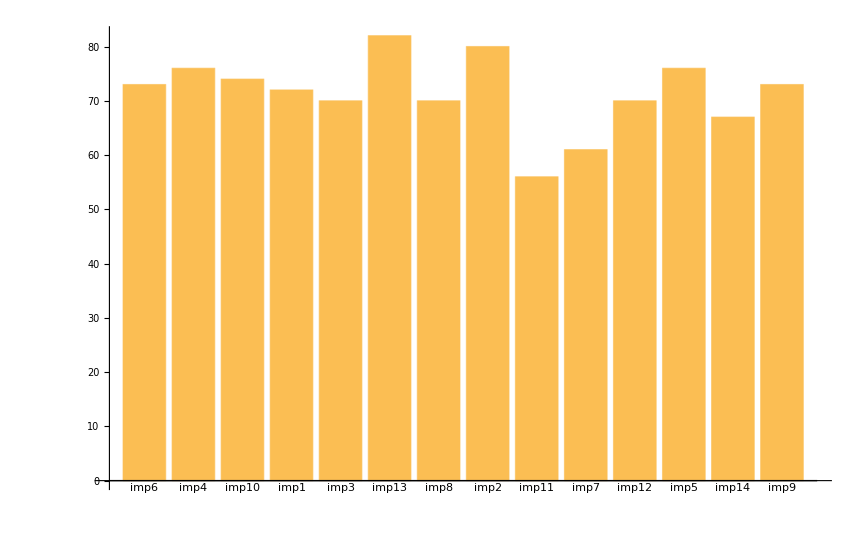

```mathematica
BarChart[Apply[Labeled,Reverse[{{imp6,73},{imp4,76},{imp10,74},{imp1,72},{imp3,70},{imp13,82},{imp8,70},{imp2,80},{imp11,56},{imp7,61},{imp12,70},{imp5,76},{imp14,67},{imp9,73}},2],{1}]]
```

```mathematica
Make[]
```

```mathematica
κ[ω_,t_,ϵ1_]:=κ[ω,t,ϵ1]=Module[{imp1=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{1,1}}->ω+ⅈ*0.001-ϵ1]]],imp2=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{2,2}}->ω+ⅈ*0.001-ϵ1]]],imp3=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{3,3}}->ω+ⅈ*0.001-ϵ1]]],imp4=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{4,4}}->ω+ⅈ*0.001-ϵ1]]],imp5=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{5,5}}->ω+ⅈ*0.001-ϵ1]]],imp7=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{7,7}}->ω+ⅈ*0.001-ϵ1]]],imp6=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{6,6}}->ω+ⅈ*0.001-ϵ1]]],imp8=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{8,8}}->ω+ⅈ*0.001-ϵ1]]],imp9=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{9,9}}->ω+ⅈ*0.001-ϵ1]]],imp10=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{10,10}}->ω+ⅈ*0.001-ϵ1]]],imp11=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{11,11}}->ω+ⅈ*0.001-ϵ1]]],imp12=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{12,12}}->ω+ⅈ*0.001-ϵ1]]],imp13=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{13,13}}->ω+ⅈ*0.001-ϵ1]]],imp14=Inverse[Module[{i=β[ω,0.001,t,0]},ReplacePart[i,{{14,14}}->ω+ⅈ*0.001-ϵ1]]]},RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp7,imp6,imp8,imp9,imp10,imp11,imp12,imp13,imp14},1000]]
```

```mathematica
Table[Re[κ[0,0.001,0,0,1][[x]]],{x,100}]
```

{1}
 |  |  |  |

```mathematica
Clear[κ]
```

```mathematica
tr33[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],T=T1[t]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[14]-κ[ω,t,ϵ1][[m]].ConjugateTranspose[T].J.T].κ[ω,t,ϵ1][[m]],{m,1,101}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.TT[1].SR[ω,δ,t,0].TT[1]].sl1;Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];
{κ[ω,t,ϵ1][[1]],η}]
```

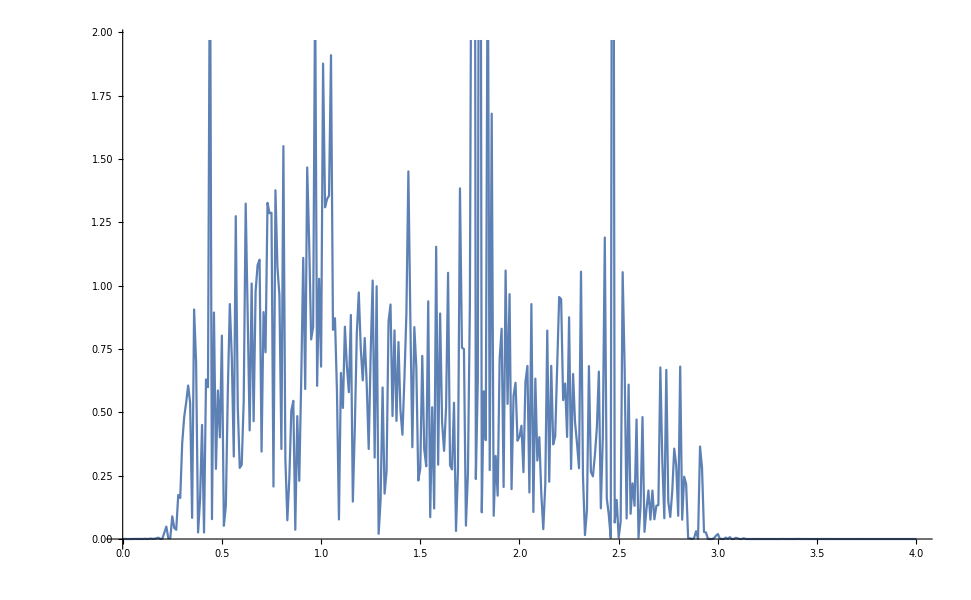

```mathematica
ListLinePlot[Table[{ω,tr33[ω,0.001,1,0,0.7][[2]]},{ω,Range[0,4,0.01]}]]
```

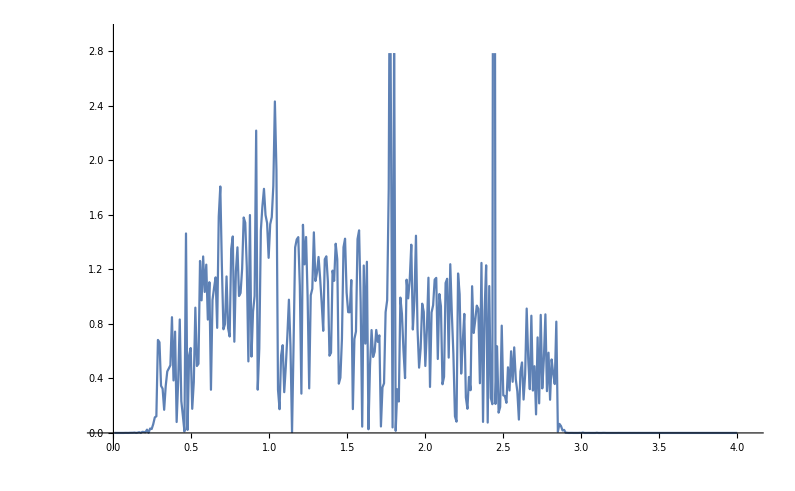

```mathematica
tr4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{imp1:=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{5,5}}->ω+ⅈ*δ-ϵ1]]],imp2:=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{7,7}}->ω+ⅈ*δ-ϵ1]]],imp3:=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{3,3}}->ω+ⅈ*δ-ϵ1]]],imp4:=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{11,11}}->ω+ⅈ*δ-ϵ1]]],imp5:=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{11,11}}->ω+ⅈ*δ-0]]],imp7:=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{14,14}}->ω+ⅈ*δ-ϵ1]]],imp6:=Inverse[Module[{i=β[ω,δ,t,ϵ]},ReplacePart[i,{{9,9}}->ω+ⅈ*δ-ϵ1]]]},η=Module[{gg=g[ω,δ,t,ϵ],κ=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp5},7]},Sl11:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].SL[ω,0.001,t,0].T1[1]].imp3;Sl12:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl11.T1[1]].imp2;Sl13:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl12.T1[1]].imp5;Sl14:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl13.T1[1]].imp3;Sl15:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl14.T1[1]].imp2;Sl16:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1]].Sl15.T1[1]].imp1;Sl17:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl16.T1[1]].imp3;Sl18:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl17.T1[1]].imp4;Sl19:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl18.T1[1]].imp5;Sl20:=Inverse[IdentityMatrix[14]-imp6.ConjugateTranspose[T1[1]].Sl19.T1[1]].imp6;Sl21:=Inverse[IdentityMatrix[14]-imp7.ConjugateTranspose[T1[1]].Sl20.T1[1]].imp7;Sl22:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl21.T1[1]].imp4;Sl23:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl22.T1[1]].imp3;Sl24:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl23.T1[1]].imp2;Sl25:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1]].Sl24.T1[1]].imp1;Sl26:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl25.T1[1]].imp4;Sl27:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl26.T1[1]].imp4;Sl28:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl27.T1[1]].imp5;Sl29:=Inverse[IdentityMatrix[14]-imp7.ConjugateTranspose[T1[1]].Sl28.T1[1]].imp7;Sl30:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl29.T1[1]].imp3;Sl31:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl30.T1[1]].imp4;Sl32:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl31.T1[1]].imp3;Sl33:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl32.T1[1]].imp3;Sl34:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl33.T1[1]].imp4;Sl35:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl34.T1[1]].imp2;Sl36:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl35.T1[1]].imp2;Sl37:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1]].Sl36.T1[1]].imp1;Sl38:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1]].Sl37.T1[1]].imp1;Sl39:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl38.T1[1]].imp4;Sl40:=Inverse[IdentityMatrix[14]-imp6.ConjugateTranspose[T1[1]].Sl39.T1[1]].imp6;Sl41:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl40.T1[1]].imp4;Sl42:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl41.T1[1]].imp5;Sl43:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl42.T1[1]].imp5;Sl44:=Inverse[IdentityMatrix[14]-imp6.ConjugateTranspose[T1[1]].Sl43.T1[1]].imp6;Sl45:=Inverse[IdentityMatrix[14]-imp7.ConjugateTranspose[T1[1]].Sl44.T1[1]].imp7;Sl46:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl45.T1[1]].imp5;Sl47:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl46.T1[1]].imp4;Sl48:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl47.T1[1]].imp3;Sl49:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl48.T1[1]].imp3;Sl50:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl49.T1[1]].imp3;Sl51:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl50.T1[1]].imp2;Sl52:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1]].Sl51.T1[1]].imp1;Sl53:=Inverse[IdentityMatrix[14]-imp6.ConjugateTranspose[T1[1]].Sl52.T1[1]].imp6;Sl54:=Inverse[IdentityMatrix[14]-imp6.ConjugateTranspose[T1[1]].Sl53.T1[1]].imp6;Sl55:=Inverse[IdentityMatrix[14]-imp7.ConjugateTranspose[T1[1]].Sl54.T1[1]].imp7;Sl56:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl55.T1[1]].imp5;Sl57:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl56.T1[1]].imp4;Sl58:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl57.T1[1]].imp3;Sl59:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl58.T1[1]].imp2;Sl60:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl59.T1[1]].imp2;Sl61:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1]].Sl60.T1[1]].imp1;Sl62:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl61.T1[1]].imp5;Sl63:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl62.T1[1]].imp5;Sl64:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl63.T1[1]].imp5;Sl65:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl64.T1[1]].imp4;Sl66:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl65.T1[1]].imp3;Sl67:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl66.T1[1]].imp3;Sl68:=Inverse[IdentityMatrix[14]-imp6.ConjugateTranspose[T1[1]].Sl67.T1[1]].imp6;Sl69:=Inverse[IdentityMatrix[14]-imp7.ConjugateTranspose[T1[1]].Sl68.T1[1]].imp7;Sl70:=Inverse[IdentityMatrix[14]-imp7.ConjugateTranspose[T1[1]].Sl69.T1[1]].imp7;Sl71:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1]].Sl70.T1[1]].imp1;Sl72:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1]].Sl71.T1[1]].imp1;Sl73:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl72.T1[1]].imp3;Sl74:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl73.T1[1]].imp2;Sl75:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl74.T1[1]].imp3;Sl76:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl75.T1[1]].imp4;Sl77:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl76.T1[1]].imp5;Sl78:=Inverse[IdentityMatrix[14]-imp6.ConjugateTranspose[T1[1]].Sl77.T1[1]].imp6;Sl79:=Inverse[IdentityMatrix[14]-imp7.ConjugateTranspose[T1[1]].Sl78.T1[1]].imp7;Sl80:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl79.T1[1]].imp4;Sl81:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1]].Sl80.T1[1]].imp3;Sl82:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl81.T1[1]].imp4;Sl83:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl82.T1[1]].imp4;Sl84:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1]].Sl83.T1[1]].imp4;Sl85:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl84.T1[1]].imp5;Sl86:=Inverse[IdentityMatrix[14]-imp5.ConjugateTranspose[T1[1]].Sl85.T1[1]].imp5;Sl87:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1]].Sl86.T1[1]].imp2;Il1:=Inverse[IdentityMatrix[14]-Sl87.TT[1].SR[ω,0.001,t,0].TT[1]].Sl87;Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].Sl87.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];{κ[[2]],Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]}];
η]
```

```mathematica
tr4[1,0.001,1,0,0.5][[2]]
```

1.70327

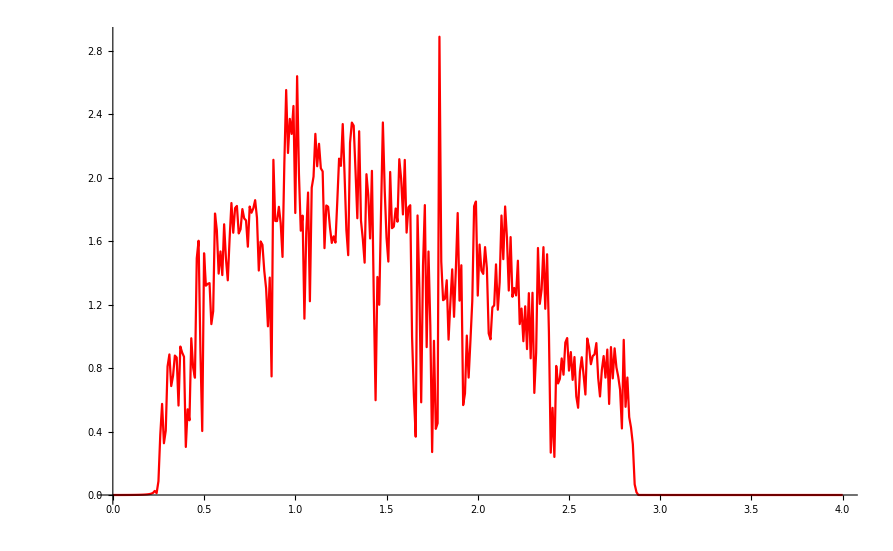

```mathematica
ListLinePlot[Table[{ω,tr4[ω,0.001,1,0,0.3][[2]]},{ω,Range[0,4,0.01]}],PlotStyle->Red]
```

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7]
```

```mathematica
{imp5,imp6,imp2,imp,imp5,imp2,imp2}
```

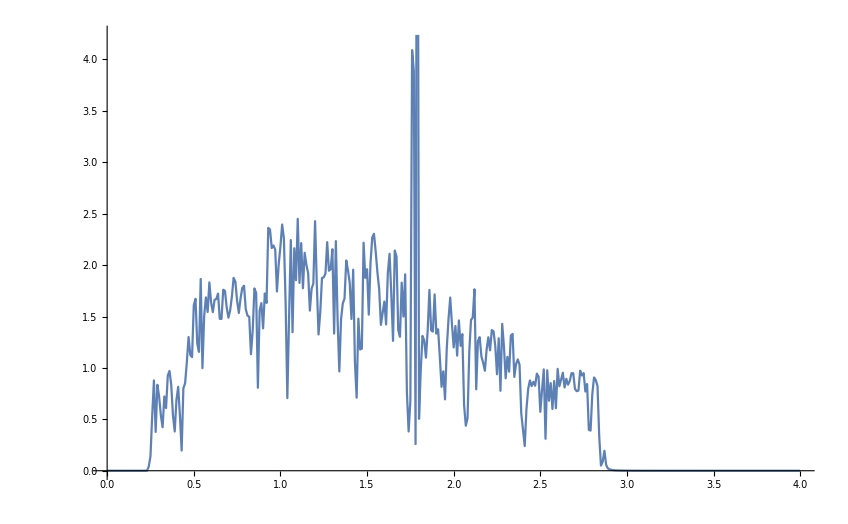

```mathematica
ListLinePlot[Table[{ω,tr4[ω,0.001,1,0,0.3][[2]]},{ω,Range[0,4,0.01]}]]
```

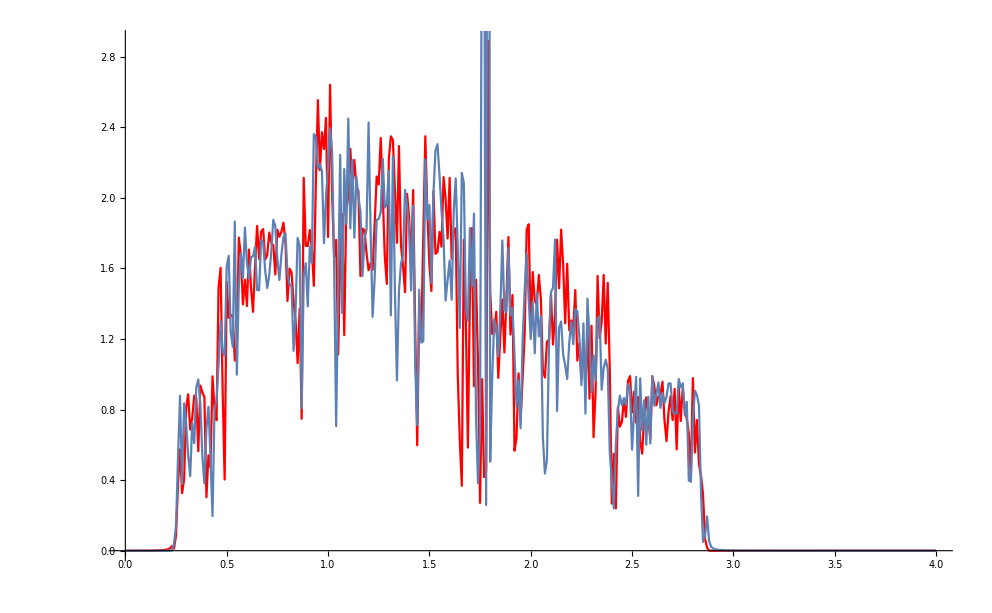

```mathematica
Show[%49,%51]
```

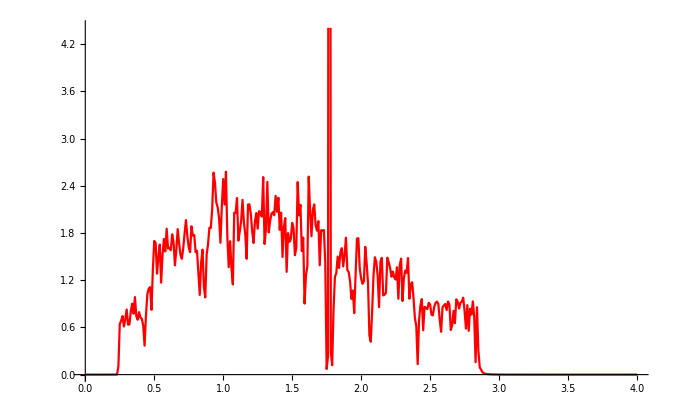

```mathematica
ListLinePlot[Table[{ω,tr4[ω,0.001,1,0,0.3][[2]]},{ω,Range[0,4,0.01]}],PlotStyle->Red]
```

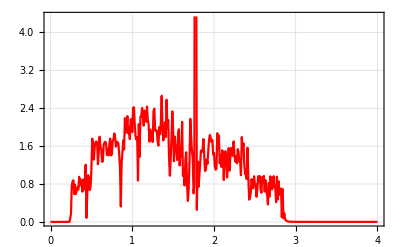

```mathematica
ListLinePlot[Table[{ω,tr4[ω,0.001,1,0,0.3]⟦2⟧},{ω,Range[0,4,0.01]}],PlotTheme->"Detailed",PlotStyle->RGBColor[1,0,0]]
```

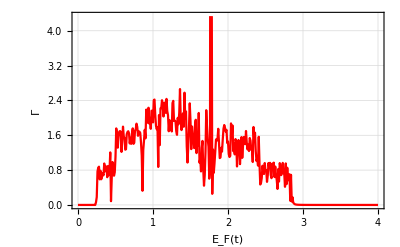

```mathematica
Show[%61,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Subscript[Ε, F][t]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

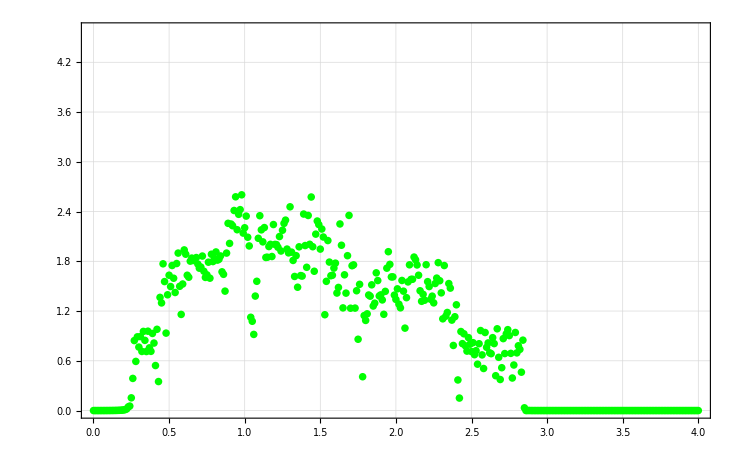

```mathematica
ListPlot[Table[{ω,tr4[ω,0.001,1,0,0.3]⟦2⟧},{ω,Range[0,4,0.01]}],PlotTheme->"Detailed",PlotStyle->Green]
```

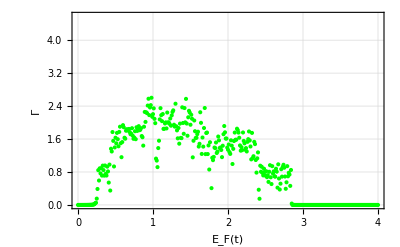

```mathematica
Show[%82,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Subscript[Ε, F][t]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

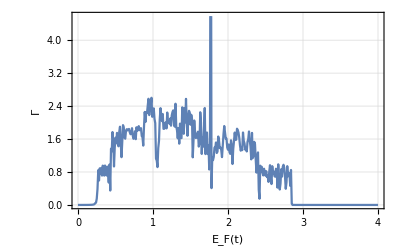

```mathematica
Show[%64,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Subscript[Ε, F][t]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

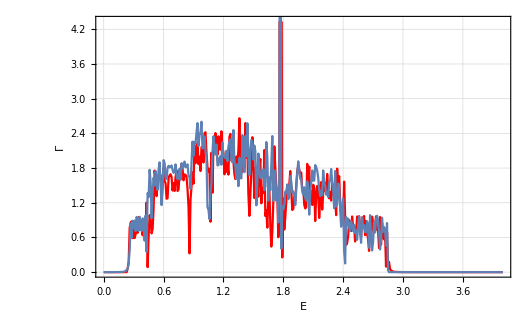

```mathematica
Show[%63,%64]
```

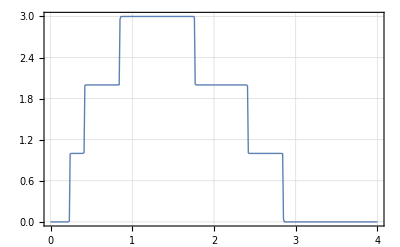

```mathematica
ListLinePlot[Table[{ω,tr4[ω,0.001,1,0,0][[2]]},{ω,Range[0,4,0.01]}],PlotStyle->Thick,PlotTheme->"Detailed"]
```

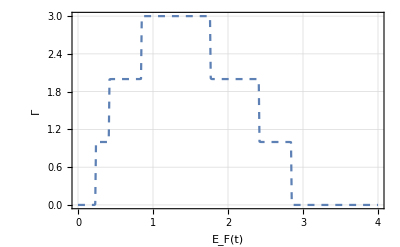

```mathematica
Show[ListLinePlot[Table[{ω,tr4[ω,0.001,1,0,0][[2]]},{ω,Range[0,4,0.01]}],PlotStyle->Dashed,PlotTheme->"Detailed"],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Subscript[Ε, F][t]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%73,%72,%71]
```

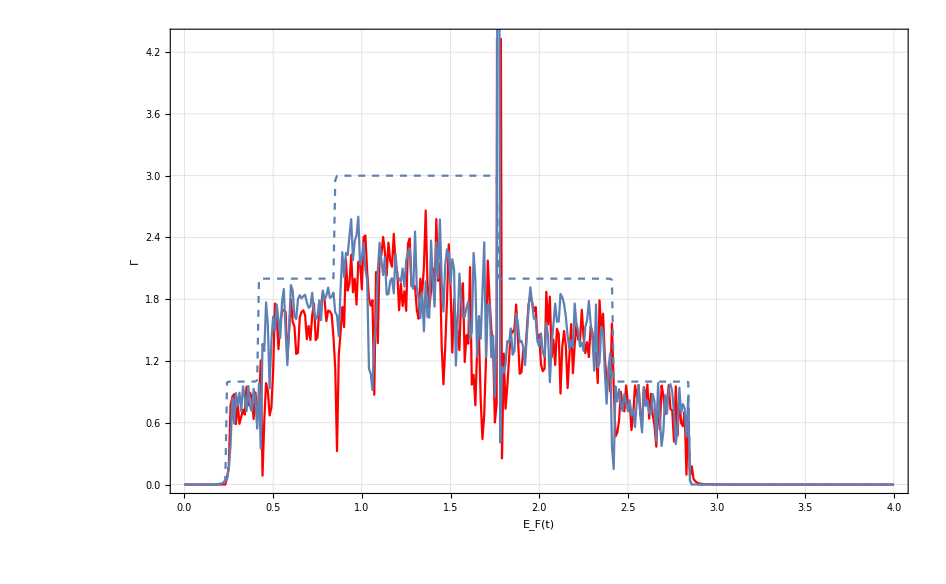

-Graphics-

```mathematica
Export["100imp.pdf",%1]
```

100imp.pdf

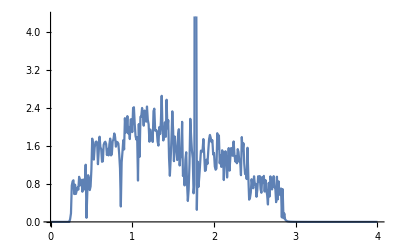

```mathematica
ListLinePlot[Table[{ω,tr4[ω,0.001,1,0,0.3][[2]]},{ω,Range[0,4,0.01]}]]
```

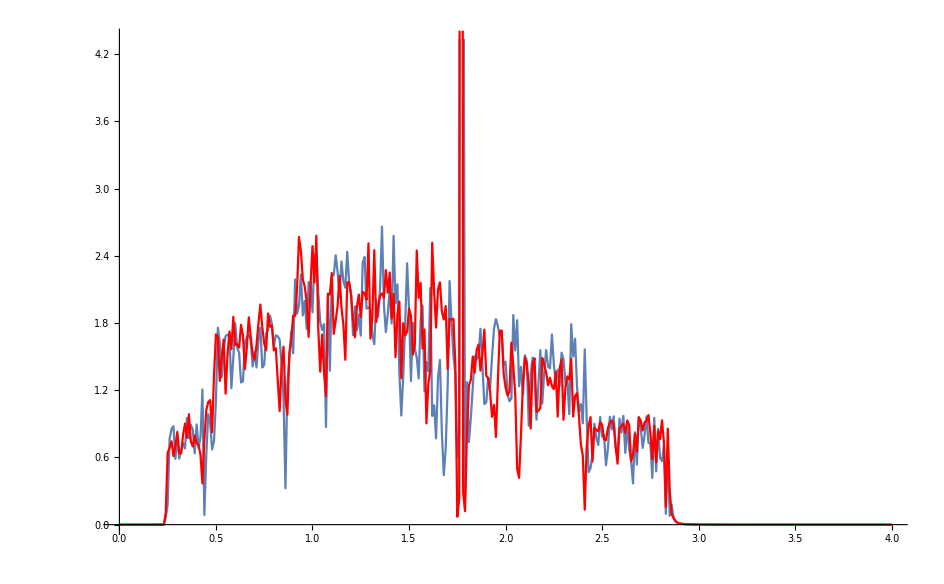

```mathematica
Show[%59,%56]
```